```mathematica
dACp=r1*cAMP*((ACt-ACp)/(Km1+(ACt-ACp)))-r2*Dt*((ACp)/Km2+ACp);
dcAMPdT=k1*ACp-k2*PDEp*cAMP;
dPDEpdT=r3*E*((PDEt-PDEp)/Km3+(PDEt-PDEp))-r4*cAMP*((PDEp)/(Km3+PDEp));
```

```mathematica
F[ACp_,cAMP_,PDEp_,ACt_,Km1_,r1_,r2_,Dt_,Km2_,k1_,k2_,E_,r3_,Km3_,r4_,PDEt_]:={dACp,dcAMPdT,dPDEpdT};
```

```mathematica
JacobianMatrix=D[F[ACp,cAMP,PDEp,ACt,Km1,r1,r2,Dt,Km2,k1,k2,E,r3,Km3,r4,PDEt],{{ACp,cAMP,PDEp}}];
JacobianMatrix
```

{{((-ACp+ACt) cAMP r1)/(-ACp+ACt+Km1)^2-(cAMP r1)/(-ACp+ACt+Km1)-Dt (1+1/Km2) r2,((-ACp+ACt) r1)/(-ACp+ACt+Km1),0},{k1,-k2 PDEp,-cAMP k2},{0,-(PDEp r4)/(Km3+PDEp),ⅇ (-1-1/Km3) r3+(cAMP PDEp r4)/(Km3+PDEp)^2-(cAMP r4)/(Km3+PDEp)}}

```mathematica
eigenvalues=Eigenvalues[JacobianMatrix];
```

```mathematica
eigenvalues
```

{Root[-ACp^6 ⅇ k1 Km2^3 Km3^8 r1 r3+6 ACp^5 ACt ⅇ k1 Km2^3 Km3^8 r1 r3-15 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^8 r1 r3+20 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^8 r1 r3-15 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^8 r1 r3+6 ACp ACt^5 ⅇ k1 Km2^3 Km3^8 r1 r3-ACt^6 ⅇ k1 Km2^3 Km3^8 r1 r3+5 ACp^5 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3-25 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^8 r1 r3+50 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3-50 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3+25 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3-5 ACt^5 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3-10 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3+40 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3-60 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3+40 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3-10 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3+10 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^8 r1 r3-30 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^8 r1 r3+30 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^8 r1 r3-10 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^8 r1 r3-5 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^8 r1 r3+10 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^8 r1 r3-5 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^8 r1 r3+ACp ⅇ k1 Km1^5 Km2^3 Km3^8 r1 r3-ACt ⅇ k1 Km1^5 Km2^3 Km3^8 r1 r3-ACp^6 ⅇ k1 Km2^3 Km3^9 r1 r3+6 ACp^5 ACt ⅇ k1 Km2^3 Km3^9 r1 r3-15 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^9 r1 r3+20 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^9 r1 r3-15 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^9 r1 r3+6 ACp ACt^5 ⅇ k1 Km2^3 Km3^9 r1 r3-ACt^6 ⅇ k1 Km2^3 Km3^9 r1 r3+5 ACp^5 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3-25 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^9 r1 r3+50 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3-50 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3+25 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3-5 ACt^5 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3-10 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3+40 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3-60 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3+40 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3-10 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3+10 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^9 r1 r3-30 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^9 r1 r3+30 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^9 r1 r3-10 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^9 r1 r3-5 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^9 r1 r3+10 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^9 r1 r3-5 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^9 r1 r3+ACp ⅇ k1 Km1^5 Km2^3 Km3^9 r1 r3-ACt ⅇ k1 Km1^5 Km2^3 Km3^9 r1 r3-6 ACp^6 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3+36 ACp^5 ACt ⅇ k1 Km2^3 Km3^7 PDEp r1 r3-90 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3+120 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3-90 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3+36 ACp ACt^5 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3-6 ACt^6 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3+30 ACp^5 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3-150 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3+300 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3-300 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3+150 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3-30 ACt^5 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3-60 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3+240 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3-360 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3+240 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3-60 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3+60 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp r1 r3-180 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp r1 r3+180 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp r1 r3-60 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp r1 r3-30 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp r1 r3+60 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp r1 r3-30 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp r1 r3+6 ACp ⅇ k1 Km1^5 Km2^3 Km3^7 PDEp r1 r3-6 ACt ⅇ k1 Km1^5 Km2^3 Km3^7 PDEp r1 r3-6 ACp^6 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3+36 ACp^5 ACt ⅇ k1 Km2^3 Km3^8 PDEp r1 r3-90 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3+120 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3-90 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3+36 ACp ACt^5 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3-6 ACt^6 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3+30 ACp^5 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3-150 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3+300 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3-300 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3+150 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3-30 ACt^5 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3+ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3-4 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3+6 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3-4 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3+ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3-60 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3+240 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3-360 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3+240 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3-60 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3-4 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r1 r3+12 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r1 r3-12 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r1 r3+4 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r1 r3+60 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^8 PDEp r1 r3-180 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^8 PDEp r1 r3+180 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^8 PDEp r1 r3-60 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^8 PDEp r1 r3+6 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r1 r3-12 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r1 r3+6 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r1 r3-30 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^8 PDEp r1 r3+60 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^8 PDEp r1 r3-30 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^8 PDEp r1 r3-4 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r1 r3+4 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r1 r3+6 ACp ⅇ k1 Km1^5 Km2^3 Km3^8 PDEp r1 r3-6 ACt ⅇ k1 Km1^5 Km2^3 Km3^8 PDEp r1 r3+cAMP ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp r1 r3+ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3-4 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3+6 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3-4 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3+ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3-4 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r1 r3+12 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r1 r3-12 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r1 r3+4 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r1 r3+6 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r1 r3-12 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r1 r3+6 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r1 r3-4 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r1 r3+4 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r1 r3+cAMP ⅇ k2 Km1^5 Km2^3 Km3^9 PDEp r1 r3-15 ACp^6 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3+90 ACp^5 ACt ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3-225 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3+300 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3-225 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3+90 ACp ACt^5 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3-15 ACt^6 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3+75 ACp^5 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3-375 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3+750 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3-750 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3+375 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3-75 ACt^5 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3-150 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3+600 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3-900 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3+600 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3-150 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3+150 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r3-450 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r3+450 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r3-150 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r3-75 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r3+150 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r3-75 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r3+15 ACp ⅇ k1 Km1^5 Km2^3 Km3^6 PDEp^2 r1 r3-15 ACt ⅇ k1 Km1^5 Km2^3 Km3^6 PDEp^2 r1 r3-15 ACp^6 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3+90 ACp^5 ACt ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3-225 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3+300 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3-225 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3+90 ACp ACt^5 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3-15 ACt^6 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3+75 ACp^5 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-375 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+750 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-750 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+375 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-75 ACt^5 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+6 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-24 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+36 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-24 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+6 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-150 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+600 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3-900 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+600 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3-150 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3-24 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+72 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3-72 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+24 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+150 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3-450 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3+450 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3-150 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3+36 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3-72 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3+36 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3-75 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3+150 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3-75 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3-24 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3+24 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3+15 ACp ⅇ k1 Km1^5 Km2^3 Km3^7 PDEp^2 r1 r3-15 ACt ⅇ k1 Km1^5 Km2^3 Km3^7 PDEp^2 r1 r3+6 cAMP ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^2 r1 r3+6 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3-24 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3+36 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3-24 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3+6 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3-24 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r1 r3+72 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r1 r3-72 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r1 r3+24 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r1 r3+36 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r1 r3-72 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r1 r3+36 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r1 r3-24 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r1 r3+24 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r1 r3+6 cAMP ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp^2 r1 r3-20 ACp^6 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3+120 ACp^5 ACt ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3-300 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3+400 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3-300 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3+120 ACp ACt^5 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3-20 ACt^6 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3+100 ACp^5 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3-500 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3+1000 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3-1000 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3+500 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3-100 ACt^5 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3-200 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3+800 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3-1200 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3+800 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3-200 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3+200 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r3-600 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r3+600 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r3-200 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r3-100 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r3+200 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r3-100 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r3+20 ACp ⅇ k1 Km1^5 Km2^3 Km3^5 PDEp^3 r1 r3-20 ACt ⅇ k1 Km1^5 Km2^3 Km3^5 PDEp^3 r1 r3-20 ACp^6 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3+120 ACp^5 ACt ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3-300 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3+400 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3-300 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3+120 ACp ACt^5 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3-20 ACt^6 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3+100 ACp^5 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-500 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+1000 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-1000 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+500 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-100 ACt^5 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+15 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-60 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+90 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-60 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+15 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-200 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+800 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3-1200 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+800 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3-200 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3-60 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+180 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3-180 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+60 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+200 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3-600 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3+600 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3-200 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3+90 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3-180 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3+90 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3-100 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3+200 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3-100 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3-60 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3+60 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3+20 ACp ⅇ k1 Km1^5 Km2^3 Km3^6 PDEp^3 r1 r3-20 ACt ⅇ k1 Km1^5 Km2^3 Km3^6 PDEp^3 r1 r3+15 cAMP ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^3 r1 r3+15 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3-60 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3+90 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3-60 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3+15 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3-60 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r1 r3+180 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r1 r3-180 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r1 r3+60 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r1 r3+90 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r1 r3-180 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r1 r3+90 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r1 r3-60 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r1 r3+60 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r1 r3+15 cAMP ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^3 r1 r3-15 ACp^6 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3+90 ACp^5 ACt ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3-225 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3+300 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3-225 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3+90 ACp ACt^5 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3-15 ACt^6 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3+75 ACp^5 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3-375 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3+750 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3-750 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3+375 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3-75 ACt^5 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3-150 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3+600 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3-900 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3+600 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3-150 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3+150 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r3-450 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r3+450 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r3-150 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r3-75 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r3+150 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r3-75 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r3+15 ACp ⅇ k1 Km1^5 Km2^3 Km3^4 PDEp^4 r1 r3-15 ACt ⅇ k1 Km1^5 Km2^3 Km3^4 PDEp^4 r1 r3-15 ACp^6 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3+90 ACp^5 ACt ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3-225 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3+300 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3-225 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3+90 ACp ACt^5 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3-15 ACt^6 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3+75 ACp^5 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-375 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+750 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-750 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+375 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-75 ACt^5 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+20 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-80 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+120 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-80 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+20 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-150 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+600 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3-900 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+600 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3-150 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3-80 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+240 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3-240 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+80 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+150 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3-450 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3+450 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3-150 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3+120 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3-240 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3+120 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3-75 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3+150 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3-75 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3-80 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3+80 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3+15 ACp ⅇ k1 Km1^5 Km2^3 Km3^5 PDEp^4 r1 r3-15 ACt ⅇ k1 Km1^5 Km2^3 Km3^5 PDEp^4 r1 r3+20 cAMP ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^4 r1 r3+20 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3-80 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3+120 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3-80 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3+20 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3-80 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r1 r3+240 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r1 r3-240 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r1 r3+80 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r1 r3+120 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r1 r3-240 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r1 r3+120 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r1 r3-80 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r1 r3+80 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r1 r3+20 cAMP ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^4 r1 r3-6 ACp^6 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3+36 ACp^5 ACt ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3-90 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3+120 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3-90 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3+36 ACp ACt^5 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3-6 ACt^6 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3+30 ACp^5 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3-150 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3+300 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3-300 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3+150 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3-30 ACt^5 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3-60 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3+240 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3-360 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3+240 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3-60 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3+60 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^5 r1 r3-180 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^5 r1 r3+180 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^5 r1 r3-60 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^5 r1 r3-30 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^5 r1 r3+60 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^5 r1 r3-30 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^5 r1 r3+6 ACp ⅇ k1 Km1^5 Km2^3 Km3^3 PDEp^5 r1 r3-6 ACt ⅇ k1 Km1^5 Km2^3 Km3^3 PDEp^5 r1 r3-6 ACp^6 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3+36 ACp^5 ACt ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3-90 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3+120 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3-90 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3+36 ACp ACt^5 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3-6 ACt^6 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3+30 ACp^5 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-150 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+300 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-300 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+150 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-30 ACt^5 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+15 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+90 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+15 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+240 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3-360 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+240 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+180 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3-180 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+60 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+60 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3-180 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3+180 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3+90 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3-180 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3+90 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3-30 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3+60 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3-30 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3+60 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3+6 ACp ⅇ k1 Km1^5 Km2^3 Km3^4 PDEp^5 r1 r3-6 ACt ⅇ k1 Km1^5 Km2^3 Km3^4 PDEp^5 r1 r3+15 cAMP ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^5 r1 r3+15 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3-60 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3+90 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3-60 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3+15 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3-60 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r1 r3+180 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r1 r3-180 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r1 r3+60 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r1 r3+90 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r1 r3-180 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r1 r3+90 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r1 r3-60 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r1 r3+60 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r1 r3+15 cAMP ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^5 r1 r3-ACp^6 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3+6 ACp^5 ACt ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3-15 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3+20 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3-15 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3+6 ACp ACt^5 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3-ACt^6 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3+5 ACp^5 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3-25 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3+50 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3-50 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3+25 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3-5 ACt^5 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3-10 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3+40 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3-60 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3+40 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3-10 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3+10 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^2 PDEp^6 r1 r3-30 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^2 PDEp^6 r1 r3+30 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^2 PDEp^6 r1 r3-10 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^2 PDEp^6 r1 r3-5 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^2 PDEp^6 r1 r3+10 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^2 PDEp^6 r1 r3-5 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^2 PDEp^6 r1 r3+ACp ⅇ k1 Km1^5 Km2^3 Km3^2 PDEp^6 r1 r3-ACt ⅇ k1 Km1^5 Km2^3 Km3^2 PDEp^6 r1 r3-ACp^6 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACp^5 ACt ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3-15 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3+20 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3-15 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACp ACt^5 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3-ACt^6 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3+5 ACp^5 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-25 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+50 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-50 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+25 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-5 ACt^5 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-24 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+36 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-24 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-10 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+40 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3-60 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+40 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3-10 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3-24 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+72 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3-72 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+24 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+10 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3-30 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3+30 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3-10 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3+36 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3-72 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3+36 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3-5 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3+10 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3-5 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3-24 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3+24 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3+ACp ⅇ k1 Km1^5 Km2^3 Km3^3 PDEp^6 r1 r3-ACt ⅇ k1 Km1^5 Km2^3 Km3^3 PDEp^6 r1 r3+6 cAMP ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3-24 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3+36 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3-24 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3+6 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3-24 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r1 r3+72 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r1 r3-72 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r1 r3+24 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r1 r3+36 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r1 r3-72 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r1 r3+36 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r1 r3-24 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r1 r3+24 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r1 r3+6 cAMP ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^6 r1 r3+ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3-4 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3+6 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3-4 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3+ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3-4 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r1 r3+12 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r1 r3-12 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r1 r3+4 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r1 r3+6 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r1 r3-12 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r1 r3+6 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r1 r3-4 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r1 r3+4 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r1 r3+cAMP ⅇ k2 Km1^5 Km2^3 Km3^2 PDEp^7 r1 r3+ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3-4 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3+6 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3-4 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3+ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3-4 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r1 r3+12 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r1 r3-12 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r1 r3+4 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r1 r3+6 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r1 r3-12 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r1 r3+6 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r1 r3-4 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r1 r3+4 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r1 r3+cAMP ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^7 r1 r3+ACp^6 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3+ACt^6 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^8 PDEp r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^8 PDEp r2 r3+Dt ⅇ k2 Km1^6 Km2^2 Km3^8 PDEp r2 r3+ACp^6 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3+ACt^6 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp r2 r3+Dt ⅇ k2 Km1^6 Km2^3 Km3^8 PDEp r2 r3+ACp^6 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3+ACt^6 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^9 PDEp r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^9 PDEp r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^9 PDEp r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^9 PDEp r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^9 PDEp r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^9 PDEp r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^9 PDEp r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^9 PDEp r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^9 PDEp r2 r3+Dt ⅇ k2 Km1^6 Km2^2 Km3^9 PDEp r2 r3+ACp^6 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3+ACt^6 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^9 PDEp r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^9 PDEp r2 r3+Dt ⅇ k2 Km1^6 Km2^3 Km3^9 PDEp r2 r3+6 ACp^6 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^7 PDEp^2 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^7 PDEp^2 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^2 Km3^7 PDEp^2 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^2 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^2 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^3 Km3^7 PDEp^2 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp^2 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp^2 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp^2 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp^2 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp^2 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^8 PDEp^2 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^8 PDEp^2 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^2 Km3^8 PDEp^2 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp^2 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp^2 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^3 Km3^8 PDEp^2 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^6 PDEp^3 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^6 PDEp^3 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^2 Km3^6 PDEp^3 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^3 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^3 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^3 Km3^6 PDEp^3 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^3 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^3 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^3 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^3 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^3 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^7 PDEp^3 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^7 PDEp^3 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^2 Km3^7 PDEp^3 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^3 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^3 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^3 Km3^7 PDEp^3 r2 r3+20 ACp^6 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3-120 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3-400 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3-120 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3+20 ACt^6 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3-120 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3+600 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3-1200 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3+1200 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3-600 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3+120 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3-1200 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3+1800 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3-1200 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3-400 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r3+1200 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r3-1200 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r3+400 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r3-600 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r3-120 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^5 PDEp^4 r2 r3+120 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^5 PDEp^4 r2 r3+20 Dt ⅇ k2 Km1^6 Km2^2 Km3^5 PDEp^4 r2 r3+20 ACp^6 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3-120 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3-400 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3-120 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3+20 ACt^6 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3-120 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3+600 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3-1200 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3+1200 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3-600 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3+120 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3-1200 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3+1800 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3-1200 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3-400 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r3+1200 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r3-1200 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r3+400 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r3-600 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r3-120 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^4 r2 r3+120 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^4 r2 r3+20 Dt ⅇ k2 Km1^6 Km2^3 Km3^5 PDEp^4 r2 r3+20 ACp^6 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3-120 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3-400 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3-120 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3+20 ACt^6 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3-120 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3+600 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3-1200 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3+1200 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3-600 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3+120 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3-1200 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3+1800 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3-1200 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3-400 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^4 r2 r3+1200 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^4 r2 r3-1200 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^4 r2 r3+400 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^4 r2 r3-600 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^4 r2 r3-120 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^6 PDEp^4 r2 r3+120 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^6 PDEp^4 r2 r3+20 Dt ⅇ k2 Km1^6 Km2^2 Km3^6 PDEp^4 r2 r3+20 ACp^6 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3-120 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3-400 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3-120 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3+20 ACt^6 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3-120 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3+600 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3-1200 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3+1200 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3-600 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3+120 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3-1200 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3+1800 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3-1200 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3-400 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r2 r3+1200 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r2 r3-1200 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r2 r3+400 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r2 r3-600 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r2 r3-120 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^4 r2 r3+120 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^4 r2 r3+20 Dt ⅇ k2 Km1^6 Km2^3 Km3^6 PDEp^4 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^4 PDEp^5 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^4 PDEp^5 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^2 Km3^4 PDEp^5 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^5 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^5 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^3 Km3^4 PDEp^5 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^5 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^5 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^5 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^5 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^5 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^5 PDEp^5 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^5 PDEp^5 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^2 Km3^5 PDEp^5 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^5 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^5 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^3 Km3^5 PDEp^5 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^3 PDEp^6 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^3 PDEp^6 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^2 Km3^3 PDEp^6 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^6 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^6 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^3 Km3^3 PDEp^6 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^6 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^6 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^6 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^6 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^6 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^4 PDEp^6 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^4 PDEp^6 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^2 Km3^4 PDEp^6 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^6 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^6 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^3 Km3^4 PDEp^6 r2 r3+ACp^6 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3+ACt^6 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^7 r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^7 r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^7 r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^2 PDEp^7 r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^2 PDEp^7 r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^2 PDEp^7 r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^2 PDEp^7 r2 r3+Dt ⅇ k2 Km1^6 Km2^2 Km3^2 PDEp^7 r2 r3+ACp^6 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3+ACt^6 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^2 PDEp^7 r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^2 PDEp^7 r2 r3+Dt ⅇ k2 Km1^6 Km2^3 Km3^2 PDEp^7 r2 r3+ACp^6 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3+ACt^6 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^7 r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^7 r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^7 r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^7 r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^7 r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^3 PDEp^7 r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^3 PDEp^7 r2 r3+Dt ⅇ k2 Km1^6 Km2^2 Km3^3 PDEp^7 r2 r3+ACp^6 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3+ACt^6 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^7 r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^7 r2 r3+Dt ⅇ k2 Km1^6 Km2^3 Km3^3 PDEp^7 r2 r3-ACp^6 cAMP k1 Km2^3 Km3^8 r1 r4+6 ACp^5 ACt cAMP k1 Km2^3 Km3^8 r1 r4-15 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^8 r1 r4+20 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^8 r1 r4-15 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^8 r1 r4+6 ACp ACt^5 cAMP k1 Km2^3 Km3^8 r1 r4-ACt^6 cAMP k1 Km2^3 Km3^8 r1 r4+5 ACp^5 cAMP k1 Km1 Km2^3 Km3^8 r1 r4-25 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^8 r1 r4+50 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^8 r1 r4-50 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^8 r1 r4+25 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^8 r1 r4-5 ACt^5 cAMP k1 Km1 Km2^3 Km3^8 r1 r4-10 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4+40 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4-60 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4+40 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4-10 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4+10 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^8 r1 r4-30 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^8 r1 r4+30 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^8 r1 r4-10 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^8 r1 r4-5 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^8 r1 r4+10 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^8 r1 r4-5 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^8 r1 r4+ACp cAMP k1 Km1^5 Km2^3 Km3^8 r1 r4-ACt cAMP k1 Km1^5 Km2^3 Km3^8 r1 r4-4 ACp^6 cAMP k1 Km2^3 Km3^7 PDEp r1 r4+24 ACp^5 ACt cAMP k1 Km2^3 Km3^7 PDEp r1 r4-60 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^7 PDEp r1 r4+80 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^7 PDEp r1 r4-60 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^7 PDEp r1 r4+24 ACp ACt^5 cAMP k1 Km2^3 Km3^7 PDEp r1 r4-4 ACt^6 cAMP k1 Km2^3 Km3^7 PDEp r1 r4+20 ACp^5 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4-100 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4+200 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4-200 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4+100 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4-20 ACt^5 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4-40 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4+160 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4-240 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4+160 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4-40 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4+40 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^7 PDEp r1 r4-120 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^7 PDEp r1 r4+120 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^7 PDEp r1 r4-40 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^7 PDEp r1 r4-20 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^7 PDEp r1 r4+40 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^7 PDEp r1 r4-20 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^7 PDEp r1 r4+4 ACp cAMP k1 Km1^5 Km2^3 Km3^7 PDEp r1 r4-4 ACt cAMP k1 Km1^5 Km2^3 Km3^7 PDEp r1 r4-6 ACp^6 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4+36 ACp^5 ACt cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4-90 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4+120 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4-90 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4+36 ACp ACt^5 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4-6 ACt^6 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4+30 ACp^5 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4-150 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4+300 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4-300 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4+150 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4-30 ACt^5 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4-60 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4+240 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4-360 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4+240 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4-60 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4+60 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r4-180 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r4+180 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r4-60 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r4-30 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r4+60 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r4-30 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r4+6 ACp cAMP k1 Km1^5 Km2^3 Km3^6 PDEp^2 r1 r4-6 ACt cAMP k1 Km1^5 Km2^3 Km3^6 PDEp^2 r1 r4-ACp^4 cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4+4 ACp^3 ACt cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4-6 ACp^2 ACt^2 cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4+4 ACp ACt^3 cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4-ACt^4 cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4+4 ACp^3 cAMP^2 k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r4-12 ACp^2 ACt cAMP^2 k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r4+12 ACp ACt^2 cAMP^2 k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r4-4 ACt^3 cAMP^2 k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r4-6 ACp^2 cAMP^2 k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r4+12 ACp ACt cAMP^2 k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r4-6 ACt^2 cAMP^2 k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r4+4 ACp cAMP^2 k2 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r4-4 ACt cAMP^2 k2 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r4-cAMP^2 k2 Km1^5 Km2^3 Km3^7 PDEp^2 r1 r4-4 ACp^6 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4+24 ACp^5 ACt cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4-60 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4+80 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4-60 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4+24 ACp ACt^5 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4-4 ACt^6 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4+20 ACp^5 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4-100 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4+200 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4-200 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4+100 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4-20 ACt^5 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4-40 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4+160 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4-240 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4+160 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4-40 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4+40 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r4-120 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r4+120 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r4-40 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r4-20 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r4+40 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r4-20 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r4+4 ACp cAMP k1 Km1^5 Km2^3 Km3^5 PDEp^3 r1 r4-4 ACt cAMP k1 Km1^5 Km2^3 Km3^5 PDEp^3 r1 r4-4 ACp^4 cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4+16 ACp^3 ACt cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4-24 ACp^2 ACt^2 cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4+16 ACp ACt^3 cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4-4 ACt^4 cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4+16 ACp^3 cAMP^2 k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r4-48 ACp^2 ACt cAMP^2 k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r4+48 ACp ACt^2 cAMP^2 k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r4-16 ACt^3 cAMP^2 k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r4-24 ACp^2 cAMP^2 k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r4+48 ACp ACt cAMP^2 k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r4-24 ACt^2 cAMP^2 k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r4+16 ACp cAMP^2 k2 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r4-16 ACt cAMP^2 k2 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r4-4 cAMP^2 k2 Km1^5 Km2^3 Km3^6 PDEp^3 r1 r4-ACp^6 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4+6 ACp^5 ACt cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4-15 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4+20 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4-15 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4+6 ACp ACt^5 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4-ACt^6 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4+5 ACp^5 cAMP k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r4-25 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r4+50 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r4-50 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r4+25 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r4-5 ACt^5 cAMP k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r4-10 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r4+40 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r4-60 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r4+40 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r4-10 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r4+10 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r4-30 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r4+30 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r4-10 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r4-5 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r4+10 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r4-5 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r4+ACp cAMP k1 Km1^5 Km2^3 Km3^4 PDEp^4 r1 r4-ACt cAMP k1 Km1^5 Km2^3 Km3^4 PDEp^4 r1 r4-6 ACp^4 cAMP^2 k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r4+24 ACp^3 ACt cAMP^2 k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r4-36 ACp^2 ACt^2 cAMP^2 k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r4+24 ACp ACt^3 cAMP^2 k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r4-6 ACt^4 cAMP^2 k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r4+24 ACp^3 cAMP^2 k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r4-72 ACp^2 ACt cAMP^2 k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r4+72 ACp ACt^2 cAMP^2 k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r4-24 ACt^3 cAMP^2 k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r4-36 ACp^2 cAMP^2 k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r4+72 ACp ACt cAMP^2 k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r4-36 ACt^2 cAMP^2 k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r4+24 ACp cAMP^2 k2 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r4-24 ACt cAMP^2 k2 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r4-6 cAMP^2 k2 Km1^5 Km2^3 Km3^5 PDEp^4 r1 r4-4 ACp^4 cAMP^2 k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r4+16 ACp^3 ACt cAMP^2 k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r4-24 ACp^2 ACt^2 cAMP^2 k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r4+16 ACp ACt^3 cAMP^2 k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r4-4 ACt^4 cAMP^2 k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r4+16 ACp^3 cAMP^2 k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r4-48 ACp^2 ACt cAMP^2 k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r4+48 ACp ACt^2 cAMP^2 k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r4-16 ACt^3 cAMP^2 k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r4-24 ACp^2 cAMP^2 k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r4+48 ACp ACt cAMP^2 k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r4-24 ACt^2 cAMP^2 k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r4+16 ACp cAMP^2 k2 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r4-16 ACt cAMP^2 k2 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r4-4 cAMP^2 k2 Km1^5 Km2^3 Km3^4 PDEp^5 r1 r4-ACp^4 cAMP^2 k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r4+4 ACp^3 ACt cAMP^2 k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r4-6 ACp^2 ACt^2 cAMP^2 k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r4+4 ACp ACt^3 cAMP^2 k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r4-ACt^4 cAMP^2 k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r4+4 ACp^3 cAMP^2 k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r4-12 ACp^2 ACt cAMP^2 k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r4+12 ACp ACt^2 cAMP^2 k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r4-4 ACt^3 cAMP^2 k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r4-6 ACp^2 cAMP^2 k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r4+12 ACp ACt cAMP^2 k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r4-6 ACt^2 cAMP^2 k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r4+4 ACp cAMP^2 k2 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r4-4 ACt cAMP^2 k2 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r4-cAMP^2 k2 Km1^5 Km2^3 Km3^3 PDEp^6 r1 r4-ACp^6 cAMP Dt k2 Km2^2 Km3^7 PDEp^2 r2 r4+6 ACp^5 ACt cAMP Dt k2 Km2^2 Km3^7 PDEp^2 r2 r4-15 ACp^4 ACt^2 cAMP Dt k2 Km2^2 Km3^7 PDEp^2 r2 r4+20 ACp^3 ACt^3 cAMP Dt k2 Km2^2 Km3^7 PDEp^2 r2 r4-15 ACp^2 ACt^4 cAMP Dt k2 Km2^2 Km3^7 PDEp^2 r2 r4+6 ACp ACt^5 cAMP Dt k2 Km2^2 Km3^7 PDEp^2 r2 r4-ACt^6 cAMP Dt k2 Km2^2 Km3^7 PDEp^2 r2 r4+6 ACp^5 cAMP Dt k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r4-30 ACp^4 ACt cAMP Dt k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r4+60 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r4-60 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r4+30 ACp ACt^4 cAMP Dt k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r4-6 ACt^5 cAMP Dt k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r4-15 ACp^4 cAMP Dt k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r4+60 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r4-90 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r4+60 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r4-15 ACt^4 cAMP Dt k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r4+20 ACp^3 cAMP Dt k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r4-60 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r4+60 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r4-20 ACt^3 cAMP Dt k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r4-15 ACp^2 cAMP Dt k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r4+30 ACp ACt cAMP Dt k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r4-15 ACt^2 cAMP Dt k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r4+6 ACp cAMP Dt k2 Km1^5 Km2^2 Km3^7 PDEp^2 r2 r4-6 ACt cAMP Dt k2 Km1^5 Km2^2 Km3^7 PDEp^2 r2 r4-cAMP Dt k2 Km1^6 Km2^2 Km3^7 PDEp^2 r2 r4-ACp^6 cAMP Dt k2 Km2^3 Km3^7 PDEp^2 r2 r4+6 ACp^5 ACt cAMP Dt k2 Km2^3 Km3^7 PDEp^2 r2 r4-15 ACp^4 ACt^2 cAMP Dt k2 Km2^3 Km3^7 PDEp^2 r2 r4+20 ACp^3 ACt^3 cAMP Dt k2 Km2^3 Km3^7 PDEp^2 r2 r4-15 ACp^2 ACt^4 cAMP Dt k2 Km2^3 Km3^7 PDEp^2 r2 r4+6 ACp ACt^5 cAMP Dt k2 Km2^3 Km3^7 PDEp^2 r2 r4-ACt^6 cAMP Dt k2 Km2^3 Km3^7 PDEp^2 r2 r4+6 ACp^5 cAMP Dt k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r4-30 ACp^4 ACt cAMP Dt k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r4+60 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r4-60 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r4+30 ACp ACt^4 cAMP Dt k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r4-6 ACt^5 cAMP Dt k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r4-15 ACp^4 cAMP Dt k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r4+60 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r4-90 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r4+60 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r4-15 ACt^4 cAMP Dt k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r4+20 ACp^3 cAMP Dt k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r4-60 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r4+60 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r4-20 ACt^3 cAMP Dt k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r4-15 ACp^2 cAMP Dt k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r4+30 ACp ACt cAMP Dt k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r4-15 ACt^2 cAMP Dt k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r4+6 ACp cAMP Dt k2 Km1^5 Km2^3 Km3^7 PDEp^2 r2 r4-6 ACt cAMP Dt k2 Km1^5 Km2^3 Km3^7 PDEp^2 r2 r4-cAMP Dt k2 Km1^6 Km2^3 Km3^7 PDEp^2 r2 r4-4 ACp^6 cAMP Dt k2 Km2^2 Km3^6 PDEp^3 r2 r4+24 ACp^5 ACt cAMP Dt k2 Km2^2 Km3^6 PDEp^3 r2 r4-60 ACp^4 ACt^2 cAMP Dt k2 Km2^2 Km3^6 PDEp^3 r2 r4+80 ACp^3 ACt^3 cAMP Dt k2 Km2^2 Km3^6 PDEp^3 r2 r4-60 ACp^2 ACt^4 cAMP Dt k2 Km2^2 Km3^6 PDEp^3 r2 r4+24 ACp ACt^5 cAMP Dt k2 Km2^2 Km3^6 PDEp^3 r2 r4-4 ACt^6 cAMP Dt k2 Km2^2 Km3^6 PDEp^3 r2 r4+24 ACp^5 cAMP Dt k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r4-120 ACp^4 ACt cAMP Dt k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r4+240 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r4-240 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r4+120 ACp ACt^4 cAMP Dt k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r4-24 ACt^5 cAMP Dt k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r4-60 ACp^4 cAMP Dt k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r4+240 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r4-360 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r4+240 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r4-60 ACt^4 cAMP Dt k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r4+80 ACp^3 cAMP Dt k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r4-240 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r4+240 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r4-80 ACt^3 cAMP Dt k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r4-60 ACp^2 cAMP Dt k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r4+120 ACp ACt cAMP Dt k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r4-60 ACt^2 cAMP Dt k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r4+24 ACp cAMP Dt k2 Km1^5 Km2^2 Km3^6 PDEp^3 r2 r4-24 ACt cAMP Dt k2 Km1^5 Km2^2 Km3^6 PDEp^3 r2 r4-4 cAMP Dt k2 Km1^6 Km2^2 Km3^6 PDEp^3 r2 r4-4 ACp^6 cAMP Dt k2 Km2^3 Km3^6 PDEp^3 r2 r4+24 ACp^5 ACt cAMP Dt k2 Km2^3 Km3^6 PDEp^3 r2 r4-60 ACp^4 ACt^2 cAMP Dt k2 Km2^3 Km3^6 PDEp^3 r2 r4+80 ACp^3 ACt^3 cAMP Dt k2 Km2^3 Km3^6 PDEp^3 r2 r4-60 ACp^2 ACt^4 cAMP Dt k2 Km2^3 Km3^6 PDEp^3 r2 r4+24 ACp ACt^5 cAMP Dt k2 Km2^3 Km3^6 PDEp^3 r2 r4-4 ACt^6 cAMP Dt k2 Km2^3 Km3^6 PDEp^3 r2 r4+24 ACp^5 cAMP Dt k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r4-120 ACp^4 ACt cAMP Dt k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r4+240 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r4-240 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r4+120 ACp ACt^4 cAMP Dt k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r4-24 ACt^5 cAMP Dt k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r4-60 ACp^4 cAMP Dt k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r4+240 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r4-360 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r4+240 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r4-60 ACt^4 cAMP Dt k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r4+80 ACp^3 cAMP Dt k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r4-240 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r4+240 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r4-80 ACt^3 cAMP Dt k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r4-60 ACp^2 cAMP Dt k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r4+120 ACp ACt cAMP Dt k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r4-60 ACt^2 cAMP Dt k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r4+24 ACp cAMP Dt k2 Km1^5 Km2^3 Km3^6 PDEp^3 r2 r4-24 ACt cAMP Dt k2 Km1^5 Km2^3 Km3^6 PDEp^3 r2 r4-4 cAMP Dt k2 Km1^6 Km2^3 Km3^6 PDEp^3 r2 r4-6 ACp^6 cAMP Dt k2 Km2^2 Km3^5 PDEp^4 r2 r4+36 ACp^5 ACt cAMP Dt k2 Km2^2 Km3^5 PDEp^4 r2 r4-90 ACp^4 ACt^2 cAMP Dt k2 Km2^2 Km3^5 PDEp^4 r2 r4+120 ACp^3 ACt^3 cAMP Dt k2 Km2^2 Km3^5 PDEp^4 r2 r4-90 ACp^2 ACt^4 cAMP Dt k2 Km2^2 Km3^5 PDEp^4 r2 r4+36 ACp ACt^5 cAMP Dt k2 Km2^2 Km3^5 PDEp^4 r2 r4-6 ACt^6 cAMP Dt k2 Km2^2 Km3^5 PDEp^4 r2 r4+36 ACp^5 cAMP Dt k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r4-180 ACp^4 ACt cAMP Dt k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r4+360 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r4-360 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r4+180 ACp ACt^4 cAMP Dt k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r4-36 ACt^5 cAMP Dt k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r4-90 ACp^4 cAMP Dt k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r4+360 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r4-540 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r4+360 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r4-90 ACt^4 cAMP Dt k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r4+120 ACp^3 cAMP Dt k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r4-360 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r4+360 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r4-120 ACt^3 cAMP Dt k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r4-90 ACp^2 cAMP Dt k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r4+180 ACp ACt cAMP Dt k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r4-90 ACt^2 cAMP Dt k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r4+36 ACp cAMP Dt k2 Km1^5 Km2^2 Km3^5 PDEp^4 r2 r4-36 ACt cAMP Dt k2 Km1^5 Km2^2 Km3^5 PDEp^4 r2 r4-6 cAMP Dt k2 Km1^6 Km2^2 Km3^5 PDEp^4 r2 r4-6 ACp^6 cAMP Dt k2 Km2^3 Km3^5 PDEp^4 r2 r4+36 ACp^5 ACt cAMP Dt k2 Km2^3 Km3^5 PDEp^4 r2 r4-90 ACp^4 ACt^2 cAMP Dt k2 Km2^3 Km3^5 PDEp^4 r2 r4+120 ACp^3 ACt^3 cAMP Dt k2 Km2^3 Km3^5 PDEp^4 r2 r4-90 ACp^2 ACt^4 cAMP Dt k2 Km2^3 Km3^5 PDEp^4 r2 r4+36 ACp ACt^5 cAMP Dt k2 Km2^3 Km3^5 PDEp^4 r2 r4-6 ACt^6 cAMP Dt k2 Km2^3 Km3^5 PDEp^4 r2 r4+36 ACp^5 cAMP Dt k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r4-180 ACp^4 ACt cAMP Dt k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r4+360 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r4-360 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r4+180 ACp ACt^4 cAMP Dt k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r4-36 ACt^5 cAMP Dt k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r4-90 ACp^4 cAMP Dt k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r4+360 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r4-540 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r4+360 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r4-90 ACt^4 cAMP Dt k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r4+120 ACp^3 cAMP Dt k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r4-360 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r4+360 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r4-120 ACt^3 cAMP Dt k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r4-90 ACp^2 cAMP Dt k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r4+180 ACp ACt cAMP Dt k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r4-90 ACt^2 cAMP Dt k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r4+36 ACp cAMP Dt k2 Km1^5 Km2^3 Km3^5 PDEp^4 r2 r4-36 ACt cAMP Dt k2 Km1^5 Km2^3 Km3^5 PDEp^4 r2 r4-6 cAMP Dt k2 Km1^6 Km2^3 Km3^5 PDEp^4 r2 r4-4 ACp^6 cAMP Dt k2 Km2^2 Km3^4 PDEp^5 r2 r4+24 ACp^5 ACt cAMP Dt k2 Km2^2 Km3^4 PDEp^5 r2 r4-60 ACp^4 ACt^2 cAMP Dt k2 Km2^2 Km3^4 PDEp^5 r2 r4+80 ACp^3 ACt^3 cAMP Dt k2 Km2^2 Km3^4 PDEp^5 r2 r4-60 ACp^2 ACt^4 cAMP Dt k2 Km2^2 Km3^4 PDEp^5 r2 r4+24 ACp ACt^5 cAMP Dt k2 Km2^2 Km3^4 PDEp^5 r2 r4-4 ACt^6 cAMP Dt k2 Km2^2 Km3^4 PDEp^5 r2 r4+24 ACp^5 cAMP Dt k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r4-120 ACp^4 ACt cAMP Dt k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r4+240 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r4-240 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r4+120 ACp ACt^4 cAMP Dt k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r4-24 ACt^5 cAMP Dt k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r4-60 ACp^4 cAMP Dt k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r4+240 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r4-360 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r4+240 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r4-60 ACt^4 cAMP Dt k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r4+80 ACp^3 cAMP Dt k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r4-240 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r4+240 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r4-80 ACt^3 cAMP Dt k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r4-60 ACp^2 cAMP Dt k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r4+120 ACp ACt cAMP Dt k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r4-60 ACt^2 cAMP Dt k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r4+24 ACp cAMP Dt k2 Km1^5 Km2^2 Km3^4 PDEp^5 r2 r4-24 ACt cAMP Dt k2 Km1^5 Km2^2 Km3^4 PDEp^5 r2 r4-4 cAMP Dt k2 Km1^6 Km2^2 Km3^4 PDEp^5 r2 r4-4 ACp^6 cAMP Dt k2 Km2^3 Km3^4 PDEp^5 r2 r4+24 ACp^5 ACt cAMP Dt k2 Km2^3 Km3^4 PDEp^5 r2 r4-60 ACp^4 ACt^2 cAMP Dt k2 Km2^3 Km3^4 PDEp^5 r2 r4+80 ACp^3 ACt^3 cAMP Dt k2 Km2^3 Km3^4 PDEp^5 r2 r4-60 ACp^2 ACt^4 cAMP Dt k2 Km2^3 Km3^4 PDEp^5 r2 r4+24 ACp ACt^5 cAMP Dt k2 Km2^3 Km3^4 PDEp^5 r2 r4-4 ACt^6 cAMP Dt k2 Km2^3 Km3^4 PDEp^5 r2 r4+24 ACp^5 cAMP Dt k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r4-120 ACp^4 ACt cAMP Dt k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r4+240 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r4-240 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r4+120 ACp ACt^4 cAMP Dt k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r4-24 ACt^5 cAMP Dt k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r4-60 ACp^4 cAMP Dt k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r4+240 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r4-360 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r4+240 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r4-60 ACt^4 cAMP Dt k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r4+80 ACp^3 cAMP Dt k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r4-240 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r4+240 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r4-80 ACt^3 cAMP Dt k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r4-60 ACp^2 cAMP Dt k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r4+120 ACp ACt cAMP Dt k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r4-60 ACt^2 cAMP Dt k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r4+24 ACp cAMP Dt k2 Km1^5 Km2^3 Km3^4 PDEp^5 r2 r4-24 ACt cAMP Dt k2 Km1^5 Km2^3 Km3^4 PDEp^5 r2 r4-4 cAMP Dt k2 Km1^6 Km2^3 Km3^4 PDEp^5 r2 r4-ACp^6 cAMP Dt k2 Km2^2 Km3^3 PDEp^6 r2 r4+6 ACp^5 ACt cAMP Dt k2 Km2^2 Km3^3 PDEp^6 r2 r4-15 ACp^4 ACt^2 cAMP Dt k2 Km2^2 Km3^3 PDEp^6 r2 r4+20 ACp^3 ACt^3 cAMP Dt k2 Km2^2 Km3^3 PDEp^6 r2 r4-15 ACp^2 ACt^4 cAMP Dt k2 Km2^2 Km3^3 PDEp^6 r2 r4+6 ACp ACt^5 cAMP Dt k2 Km2^2 Km3^3 PDEp^6 r2 r4-ACt^6 cAMP Dt k2 Km2^2 Km3^3 PDEp^6 r2 r4+6 ACp^5 cAMP Dt k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r4-30 ACp^4 ACt cAMP Dt k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r4+60 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r4-60 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r4+30 ACp ACt^4 cAMP Dt k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r4-6 ACt^5 cAMP Dt k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r4-15 ACp^4 cAMP Dt k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r4+60 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r4-90 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r4+60 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r4-15 ACt^4 cAMP Dt k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r4+20 ACp^3 cAMP Dt k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r4-60 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r4+60 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r4-20 ACt^3 cAMP Dt k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r4-15 ACp^2 cAMP Dt k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r4+30 ACp ACt cAMP Dt k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r4-15 ACt^2 cAMP Dt k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r4+6 ACp cAMP Dt k2 Km1^5 Km2^2 Km3^3 PDEp^6 r2 r4-6 ACt cAMP Dt k2 Km1^5 Km2^2 Km3^3 PDEp^6 r2 r4-cAMP Dt k2 Km1^6 Km2^2 Km3^3 PDEp^6 r2 r4-ACp^6 cAMP Dt k2 Km2^3 Km3^3 PDEp^6 r2 r4+6 ACp^5 ACt cAMP Dt k2 Km2^3 Km3^3 PDEp^6 r2 r4-15 ACp^4 ACt^2 cAMP Dt k2 Km2^3 Km3^3 PDEp^6 r2 r4+20 ACp^3 ACt^3 cAMP Dt k2 Km2^3 Km3^3 PDEp^6 r2 r4-15 ACp^2 ACt^4 cAMP Dt k2 Km2^3 Km3^3 PDEp^6 r2 r4+6 ACp ACt^5 cAMP Dt k2 Km2^3 Km3^3 PDEp^6 r2 r4-ACt^6 cAMP Dt k2 Km2^3 Km3^3 PDEp^6 r2 r4+6 ACp^5 cAMP Dt k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r4-30 ACp^4 ACt cAMP Dt k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r4+60 ACp^3 ACt^2 cAMP Dt k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r4-60 ACp^2 ACt^3 cAMP Dt k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r4+30 ACp ACt^4 cAMP Dt k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r4-6 ACt^5 cAMP Dt k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r4-15 ACp^4 cAMP Dt k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r4+60 ACp^3 ACt cAMP Dt k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r4-90 ACp^2 ACt^2 cAMP Dt k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r4+60 ACp ACt^3 cAMP Dt k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r4-15 ACt^4 cAMP Dt k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r4+20 ACp^3 cAMP Dt k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r4-60 ACp^2 ACt cAMP Dt k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r4+60 ACp ACt^2 cAMP Dt k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r4-20 ACt^3 cAMP Dt k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r4-15 ACp^2 cAMP Dt k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r4+30 ACp ACt cAMP Dt k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r4-15 ACt^2 cAMP Dt k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r4+6 ACp cAMP Dt k2 Km1^5 Km2^3 Km3^3 PDEp^6 r2 r4-6 ACt cAMP Dt k2 Km1^5 Km2^3 Km3^3 PDEp^6 r2 r4-cAMP Dt k2 Km1^6 Km2^3 Km3^3 PDEp^6 r2 r4+(-ACp^4 k1 Km2^2 Km3^6 r1+4 ACp^3 ACt k1 Km2^2 Km3^6 r1-6 ACp^2 ACt^2 k1 Km2^2 Km3^6 r1+4 ACp ACt^3 k1 Km2^2 Km3^6 r1-ACt^4 k1 Km2^2 Km3^6 r1+3 ACp^3 k1 Km1 Km2^2 Km3^6 r1-9 ACp^2 ACt k1 Km1 Km2^2 Km3^6 r1+9 ACp ACt^2 k1 Km1 Km2^2 Km3^6 r1-3 ACt^3 k1 Km1 Km2^2 Km3^6 r1-3 ACp^2 k1 Km1^2 Km2^2 Km3^6 r1+6 ACp ACt k1 Km1^2 Km2^2 Km3^6 r1-3 ACt^2 k1 Km1^2 Km2^2 Km3^6 r1+ACp k1 Km1^3 Km2^2 Km3^6 r1-ACt k1 Km1^3 Km2^2 Km3^6 r1-4 ACp^4 k1 Km2^2 Km3^5 PDEp r1+16 ACp^3 ACt k1 Km2^2 Km3^5 PDEp r1-24 ACp^2 ACt^2 k1 Km2^2 Km3^5 PDEp r1+16 ACp ACt^3 k1 Km2^2 Km3^5 PDEp r1-4 ACt^4 k1 Km2^2 Km3^5 PDEp r1+12 ACp^3 k1 Km1 Km2^2 Km3^5 PDEp r1-36 ACp^2 ACt k1 Km1 Km2^2 Km3^5 PDEp r1+36 ACp ACt^2 k1 Km1 Km2^2 Km3^5 PDEp r1-12 ACt^3 k1 Km1 Km2^2 Km3^5 PDEp r1-12 ACp^2 k1 Km1^2 Km2^2 Km3^5 PDEp r1+24 ACp ACt k1 Km1^2 Km2^2 Km3^5 PDEp r1-12 ACt^2 k1 Km1^2 Km2^2 Km3^5 PDEp r1+4 ACp k1 Km1^3 Km2^2 Km3^5 PDEp r1-4 ACt k1 Km1^3 Km2^2 Km3^5 PDEp r1+ACp^2 cAMP k2 Km1 Km2^2 Km3^6 PDEp r1-2 ACp ACt cAMP k2 Km1 Km2^2 Km3^6 PDEp r1+ACt^2 cAMP k2 Km1 Km2^2 Km3^6 PDEp r1-2 ACp cAMP k2 Km1^2 Km2^2 Km3^6 PDEp r1+2 ACt cAMP k2 Km1^2 Km2^2 Km3^6 PDEp r1+cAMP k2 Km1^3 Km2^2 Km3^6 PDEp r1-6 ACp^4 k1 Km2^2 Km3^4 PDEp^2 r1+24 ACp^3 ACt k1 Km2^2 Km3^4 PDEp^2 r1-36 ACp^2 ACt^2 k1 Km2^2 Km3^4 PDEp^2 r1+24 ACp ACt^3 k1 Km2^2 Km3^4 PDEp^2 r1-6 ACt^4 k1 Km2^2 Km3^4 PDEp^2 r1+18 ACp^3 k1 Km1 Km2^2 Km3^4 PDEp^2 r1-54 ACp^2 ACt k1 Km1 Km2^2 Km3^4 PDEp^2 r1+54 ACp ACt^2 k1 Km1 Km2^2 Km3^4 PDEp^2 r1-18 ACt^3 k1 Km1 Km2^2 Km3^4 PDEp^2 r1-18 ACp^2 k1 Km1^2 Km2^2 Km3^4 PDEp^2 r1+36 ACp ACt k1 Km1^2 Km2^2 Km3^4 PDEp^2 r1-18 ACt^2 k1 Km1^2 Km2^2 Km3^4 PDEp^2 r1+6 ACp k1 Km1^3 Km2^2 Km3^4 PDEp^2 r1-6 ACt k1 Km1^3 Km2^2 Km3^4 PDEp^2 r1+4 ACp^2 cAMP k2 Km1 Km2^2 Km3^5 PDEp^2 r1-8 ACp ACt cAMP k2 Km1 Km2^2 Km3^5 PDEp^2 r1+4 ACt^2 cAMP k2 Km1 Km2^2 Km3^5 PDEp^2 r1-8 ACp cAMP k2 Km1^2 Km2^2 Km3^5 PDEp^2 r1+8 ACt cAMP k2 Km1^2 Km2^2 Km3^5 PDEp^2 r1+4 cAMP k2 Km1^3 Km2^2 Km3^5 PDEp^2 r1-4 ACp^4 k1 Km2^2 Km3^3 PDEp^3 r1+16 ACp^3 ACt k1 Km2^2 Km3^3 PDEp^3 r1-24 ACp^2 ACt^2 k1 Km2^2 Km3^3 PDEp^3 r1+16 ACp ACt^3 k1 Km2^2 Km3^3 PDEp^3 r1-4 ACt^4 k1 Km2^2 Km3^3 PDEp^3 r1+12 ACp^3 k1 Km1 Km2^2 Km3^3 PDEp^3 r1-36 ACp^2 ACt k1 Km1 Km2^2 Km3^3 PDEp^3 r1+36 ACp ACt^2 k1 Km1 Km2^2 Km3^3 PDEp^3 r1-12 ACt^3 k1 Km1 Km2^2 Km3^3 PDEp^3 r1-12 ACp^2 k1 Km1^2 Km2^2 Km3^3 PDEp^3 r1+24 ACp ACt k1 Km1^2 Km2^2 Km3^3 PDEp^3 r1-12 ACt^2 k1 Km1^2 Km2^2 Km3^3 PDEp^3 r1+4 ACp k1 Km1^3 Km2^2 Km3^3 PDEp^3 r1-4 ACt k1 Km1^3 Km2^2 Km3^3 PDEp^3 r1+6 ACp^2 cAMP k2 Km1 Km2^2 Km3^4 PDEp^3 r1-12 ACp ACt cAMP k2 Km1 Km2^2 Km3^4 PDEp^3 r1+6 ACt^2 cAMP k2 Km1 Km2^2 Km3^4 PDEp^3 r1-12 ACp cAMP k2 Km1^2 Km2^2 Km3^4 PDEp^3 r1+12 ACt cAMP k2 Km1^2 Km2^2 Km3^4 PDEp^3 r1+6 cAMP k2 Km1^3 Km2^2 Km3^4 PDEp^3 r1-ACp^4 k1 Km2^2 Km3^2 PDEp^4 r1+4 ACp^3 ACt k1 Km2^2 Km3^2 PDEp^4 r1-6 ACp^2 ACt^2 k1 Km2^2 Km3^2 PDEp^4 r1+4 ACp ACt^3 k1 Km2^2 Km3^2 PDEp^4 r1-ACt^4 k1 Km2^2 Km3^2 PDEp^4 r1+3 ACp^3 k1 Km1 Km2^2 Km3^2 PDEp^4 r1-9 ACp^2 ACt k1 Km1 Km2^2 Km3^2 PDEp^4 r1+9 ACp ACt^2 k1 Km1 Km2^2 Km3^2 PDEp^4 r1-3 ACt^3 k1 Km1 Km2^2 Km3^2 PDEp^4 r1-3 ACp^2 k1 Km1^2 Km2^2 Km3^2 PDEp^4 r1+6 ACp ACt k1 Km1^2 Km2^2 Km3^2 PDEp^4 r1-3 ACt^2 k1 Km1^2 Km2^2 Km3^2 PDEp^4 r1+ACp k1 Km1^3 Km2^2 Km3^2 PDEp^4 r1-ACt k1 Km1^3 Km2^2 Km3^2 PDEp^4 r1+4 ACp^2 cAMP k2 Km1 Km2^2 Km3^3 PDEp^4 r1-8 ACp ACt cAMP k2 Km1 Km2^2 Km3^3 PDEp^4 r1+4 ACt^2 cAMP k2 Km1 Km2^2 Km3^3 PDEp^4 r1-8 ACp cAMP k2 Km1^2 Km2^2 Km3^3 PDEp^4 r1+8 ACt cAMP k2 Km1^2 Km2^2 Km3^3 PDEp^4 r1+4 cAMP k2 Km1^3 Km2^2 Km3^3 PDEp^4 r1+ACp^2 cAMP k2 Km1 Km2^2 Km3^2 PDEp^5 r1-2 ACp ACt cAMP k2 Km1 Km2^2 Km3^2 PDEp^5 r1+ACt^2 cAMP k2 Km1 Km2^2 Km3^2 PDEp^5 r1-2 ACp cAMP k2 Km1^2 Km2^2 Km3^2 PDEp^5 r1+2 ACt cAMP k2 Km1^2 Km2^2 Km3^2 PDEp^5 r1+cAMP k2 Km1^3 Km2^2 Km3^2 PDEp^5 r1+ACp^4 Dt k2 Km2 Km3^6 PDEp r2-4 ACp^3 ACt Dt k2 Km2 Km3^6 PDEp r2+6 ACp^2 ACt^2 Dt k2 Km2 Km3^6 PDEp r2-4 ACp ACt^3 Dt k2 Km2 Km3^6 PDEp r2+ACt^4 Dt k2 Km2 Km3^6 PDEp r2-4 ACp^3 Dt k2 Km1 Km2 Km3^6 PDEp r2+12 ACp^2 ACt Dt k2 Km1 Km2 Km3^6 PDEp r2-12 ACp ACt^2 Dt k2 Km1 Km2 Km3^6 PDEp r2+4 ACt^3 Dt k2 Km1 Km2 Km3^6 PDEp r2+6 ACp^2 Dt k2 Km1^2 Km2 Km3^6 PDEp r2-12 ACp ACt Dt k2 Km1^2 Km2 Km3^6 PDEp r2+6 ACt^2 Dt k2 Km1^2 Km2 Km3^6 PDEp r2-4 ACp Dt k2 Km1^3 Km2 Km3^6 PDEp r2+4 ACt Dt k2 Km1^3 Km2 Km3^6 PDEp r2+Dt k2 Km1^4 Km2 Km3^6 PDEp r2+ACp^4 Dt k2 Km2^2 Km3^6 PDEp r2-4 ACp^3 ACt Dt k2 Km2^2 Km3^6 PDEp r2+6 ACp^2 ACt^2 Dt k2 Km2^2 Km3^6 PDEp r2-4 ACp ACt^3 Dt k2 Km2^2 Km3^6 PDEp r2+ACt^4 Dt k2 Km2^2 Km3^6 PDEp r2-4 ACp^3 Dt k2 Km1 Km2^2 Km3^6 PDEp r2+12 ACp^2 ACt Dt k2 Km1 Km2^2 Km3^6 PDEp r2-12 ACp ACt^2 Dt k2 Km1 Km2^2 Km3^6 PDEp r2+4 ACt^3 Dt k2 Km1 Km2^2 Km3^6 PDEp r2+6 ACp^2 Dt k2 Km1^2 Km2^2 Km3^6 PDEp r2-12 ACp ACt Dt k2 Km1^2 Km2^2 Km3^6 PDEp r2+6 ACt^2 Dt k2 Km1^2 Km2^2 Km3^6 PDEp r2-4 ACp Dt k2 Km1^3 Km2^2 Km3^6 PDEp r2+4 ACt Dt k2 Km1^3 Km2^2 Km3^6 PDEp r2+Dt k2 Km1^4 Km2^2 Km3^6 PDEp r2+4 ACp^4 Dt k2 Km2 Km3^5 PDEp^2 r2-16 ACp^3 ACt Dt k2 Km2 Km3^5 PDEp^2 r2+24 ACp^2 ACt^2 Dt k2 Km2 Km3^5 PDEp^2 r2-16 ACp ACt^3 Dt k2 Km2 Km3^5 PDEp^2 r2+4 ACt^4 Dt k2 Km2 Km3^5 PDEp^2 r2-16 ACp^3 Dt k2 Km1 Km2 Km3^5 PDEp^2 r2+48 ACp^2 ACt Dt k2 Km1 Km2 Km3^5 PDEp^2 r2-48 ACp ACt^2 Dt k2 Km1 Km2 Km3^5 PDEp^2 r2+16 ACt^3 Dt k2 Km1 Km2 Km3^5 PDEp^2 r2+24 ACp^2 Dt k2 Km1^2 Km2 Km3^5 PDEp^2 r2-48 ACp ACt Dt k2 Km1^2 Km2 Km3^5 PDEp^2 r2+24 ACt^2 Dt k2 Km1^2 Km2 Km3^5 PDEp^2 r2-16 ACp Dt k2 Km1^3 Km2 Km3^5 PDEp^2 r2+16 ACt Dt k2 Km1^3 Km2 Km3^5 PDEp^2 r2+4 Dt k2 Km1^4 Km2 Km3^5 PDEp^2 r2+4 ACp^4 Dt k2 Km2^2 Km3^5 PDEp^2 r2-16 ACp^3 ACt Dt k2 Km2^2 Km3^5 PDEp^2 r2+24 ACp^2 ACt^2 Dt k2 Km2^2 Km3^5 PDEp^2 r2-16 ACp ACt^3 Dt k2 Km2^2 Km3^5 PDEp^2 r2+4 ACt^4 Dt k2 Km2^2 Km3^5 PDEp^2 r2-16 ACp^3 Dt k2 Km1 Km2^2 Km3^5 PDEp^2 r2+48 ACp^2 ACt Dt k2 Km1 Km2^2 Km3^5 PDEp^2 r2-48 ACp ACt^2 Dt k2 Km1 Km2^2 Km3^5 PDEp^2 r2+16 ACt^3 Dt k2 Km1 Km2^2 Km3^5 PDEp^2 r2+24 ACp^2 Dt k2 Km1^2 Km2^2 Km3^5 PDEp^2 r2-48 ACp ACt Dt k2 Km1^2 Km2^2 Km3^5 PDEp^2 r2+24 ACt^2 Dt k2 Km1^2 Km2^2 Km3^5 PDEp^2 r2-16 ACp Dt k2 Km1^3 Km2^2 Km3^5 PDEp^2 r2+16 ACt Dt k2 Km1^3 Km2^2 Km3^5 PDEp^2 r2+4 Dt k2 Km1^4 Km2^2 Km3^5 PDEp^2 r2+6 ACp^4 Dt k2 Km2 Km3^4 PDEp^3 r2-24 ACp^3 ACt Dt k2 Km2 Km3^4 PDEp^3 r2+36 ACp^2 ACt^2 Dt k2 Km2 Km3^4 PDEp^3 r2-24 ACp ACt^3 Dt k2 Km2 Km3^4 PDEp^3 r2+6 ACt^4 Dt k2 Km2 Km3^4 PDEp^3 r2-24 ACp^3 Dt k2 Km1 Km2 Km3^4 PDEp^3 r2+72 ACp^2 ACt Dt k2 Km1 Km2 Km3^4 PDEp^3 r2-72 ACp ACt^2 Dt k2 Km1 Km2 Km3^4 PDEp^3 r2+24 ACt^3 Dt k2 Km1 Km2 Km3^4 PDEp^3 r2+36 ACp^2 Dt k2 Km1^2 Km2 Km3^4 PDEp^3 r2-72 ACp ACt Dt k2 Km1^2 Km2 Km3^4 PDEp^3 r2+36 ACt^2 Dt k2 Km1^2 Km2 Km3^4 PDEp^3 r2-24 ACp Dt k2 Km1^3 Km2 Km3^4 PDEp^3 r2+24 ACt Dt k2 Km1^3 Km2 Km3^4 PDEp^3 r2+6 Dt k2 Km1^4 Km2 Km3^4 PDEp^3 r2+6 ACp^4 Dt k2 Km2^2 Km3^4 PDEp^3 r2-24 ACp^3 ACt Dt k2 Km2^2 Km3^4 PDEp^3 r2+36 ACp^2 ACt^2 Dt k2 Km2^2 Km3^4 PDEp^3 r2-24 ACp ACt^3 Dt k2 Km2^2 Km3^4 PDEp^3 r2+6 ACt^4 Dt k2 Km2^2 Km3^4 PDEp^3 r2-24 ACp^3 Dt k2 Km1 Km2^2 Km3^4 PDEp^3 r2+72 ACp^2 ACt Dt k2 Km1 Km2^2 Km3^4 PDEp^3 r2-72 ACp ACt^2 Dt k2 Km1 Km2^2 Km3^4 PDEp^3 r2+24 ACt^3 Dt k2 Km1 Km2^2 Km3^4 PDEp^3 r2+36 ACp^2 Dt k2 Km1^2 Km2^2 Km3^4 PDEp^3 r2-72 ACp ACt Dt k2 Km1^2 Km2^2 Km3^4 PDEp^3 r2+36 ACt^2 Dt k2 Km1^2 Km2^2 Km3^4 PDEp^3 r2-24 ACp Dt k2 Km1^3 Km2^2 Km3^4 PDEp^3 r2+24 ACt Dt k2 Km1^3 Km2^2 Km3^4 PDEp^3 r2+6 Dt k2 Km1^4 Km2^2 Km3^4 PDEp^3 r2+4 ACp^4 Dt k2 Km2 Km3^3 PDEp^4 r2-16 ACp^3 ACt Dt k2 Km2 Km3^3 PDEp^4 r2+24 ACp^2 ACt^2 Dt k2 Km2 Km3^3 PDEp^4 r2-16 ACp ACt^3 Dt k2 Km2 Km3^3 PDEp^4 r2+4 ACt^4 Dt k2 Km2 Km3^3 PDEp^4 r2-16 ACp^3 Dt k2 Km1 Km2 Km3^3 PDEp^4 r2+48 ACp^2 ACt Dt k2 Km1 Km2 Km3^3 PDEp^4 r2-48 ACp ACt^2 Dt k2 Km1 Km2 Km3^3 PDEp^4 r2+16 ACt^3 Dt k2 Km1 Km2 Km3^3 PDEp^4 r2+24 ACp^2 Dt k2 Km1^2 Km2 Km3^3 PDEp^4 r2-48 ACp ACt Dt k2 Km1^2 Km2 Km3^3 PDEp^4 r2+24 ACt^2 Dt k2 Km1^2 Km2 Km3^3 PDEp^4 r2-16 ACp Dt k2 Km1^3 Km2 Km3^3 PDEp^4 r2+16 ACt Dt k2 Km1^3 Km2 Km3^3 PDEp^4 r2+4 Dt k2 Km1^4 Km2 Km3^3 PDEp^4 r2+4 ACp^4 Dt k2 Km2^2 Km3^3 PDEp^4 r2-16 ACp^3 ACt Dt k2 Km2^2 Km3^3 PDEp^4 r2+24 ACp^2 ACt^2 Dt k2 Km2^2 Km3^3 PDEp^4 r2-16 ACp ACt^3 Dt k2 Km2^2 Km3^3 PDEp^4 r2+4 ACt^4 Dt k2 Km2^2 Km3^3 PDEp^4 r2-16 ACp^3 Dt k2 Km1 Km2^2 Km3^3 PDEp^4 r2+48 ACp^2 ACt Dt k2 Km1 Km2^2 Km3^3 PDEp^4 r2-48 ACp ACt^2 Dt k2 Km1 Km2^2 Km3^3 PDEp^4 r2+16 ACt^3 Dt k2 Km1 Km2^2 Km3^3 PDEp^4 r2+24 ACp^2 Dt k2 Km1^2 Km2^2 Km3^3 PDEp^4 r2-48 ACp ACt Dt k2 Km1^2 Km2^2 Km3^3 PDEp^4 r2+24 ACt^2 Dt k2 Km1^2 Km2^2 Km3^3 PDEp^4 r2-16 ACp Dt k2 Km1^3 Km2^2 Km3^3 PDEp^4 r2+16 ACt Dt k2 Km1^3 Km2^2 Km3^3 PDEp^4 r2+4 Dt k2 Km1^4 Km2^2 Km3^3 PDEp^4 r2+ACp^4 Dt k2 Km2 Km3^2 PDEp^5 r2-4 ACp^3 ACt Dt k2 Km2 Km3^2 PDEp^5 r2+6 ACp^2 ACt^2 Dt k2 Km2 Km3^2 PDEp^5 r2-4 ACp ACt^3 Dt k2 Km2 Km3^2 PDEp^5 r2+ACt^4 Dt k2 Km2 Km3^2 PDEp^5 r2-4 ACp^3 Dt k2 Km1 Km2 Km3^2 PDEp^5 r2+12 ACp^2 ACt Dt k2 Km1 Km2 Km3^2 PDEp^5 r2-12 ACp ACt^2 Dt k2 Km1 Km2 Km3^2 PDEp^5 r2+4 ACt^3 Dt k2 Km1 Km2 Km3^2 PDEp^5 r2+6 ACp^2 Dt k2 Km1^2 Km2 Km3^2 PDEp^5 r2-12 ACp ACt Dt k2 Km1^2 Km2 Km3^2 PDEp^5 r2+6 ACt^2 Dt k2 Km1^2 Km2 Km3^2 PDEp^5 r2-4 ACp Dt k2 Km1^3 Km2 Km3^2 PDEp^5 r2+4 ACt Dt k2 Km1^3 Km2 Km3^2 PDEp^5 r2+Dt k2 Km1^4 Km2 Km3^2 PDEp^5 r2+ACp^4 Dt k2 Km2^2 Km3^2 PDEp^5 r2-4 ACp^3 ACt Dt k2 Km2^2 Km3^2 PDEp^5 r2+6 ACp^2 ACt^2 Dt k2 Km2^2 Km3^2 PDEp^5 r2-4 ACp ACt^3 Dt k2 Km2^2 Km3^2 PDEp^5 r2+ACt^4 Dt k2 Km2^2 Km3^2 PDEp^5 r2-4 ACp^3 Dt k2 Km1 Km2^2 Km3^2 PDEp^5 r2+12 ACp^2 ACt Dt k2 Km1 Km2^2 Km3^2 PDEp^5 r2-12 ACp ACt^2 Dt k2 Km1 Km2^2 Km3^2 PDEp^5 r2+4 ACt^3 Dt k2 Km1 Km2^2 Km3^2 PDEp^5 r2+6 ACp^2 Dt k2 Km1^2 Km2^2 Km3^2 PDEp^5 r2-12 ACp ACt Dt k2 Km1^2 Km2^2 Km3^2 PDEp^5 r2+6 ACt^2 Dt k2 Km1^2 Km2^2 Km3^2 PDEp^5 r2-4 ACp Dt k2 Km1^3 Km2^2 Km3^2 PDEp^5 r2+4 ACt Dt k2 Km1^3 Km2^2 Km3^2 PDEp^5 r2+Dt k2 Km1^4 Km2^2 Km3^2 PDEp^5 r2+ACp^4 ⅇ k2 Km2^2 Km3^5 PDEp r3-4 ACp^3 ACt ⅇ k2 Km2^2 Km3^5 PDEp r3+6 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^5 PDEp r3-4 ACp ACt^3 ⅇ k2 Km2^2 Km3^5 PDEp r3+ACt^4 ⅇ k2 Km2^2 Km3^5 PDEp r3-4 ACp^3 ⅇ k2 Km1 Km2^2 Km3^5 PDEp r3+12 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^5 PDEp r3-12 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^5 PDEp r3+4 ACt^3 ⅇ k2 Km1 Km2^2 Km3^5 PDEp r3+6 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp r3-12 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp r3+6 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp r3-4 ACp ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp r3+4 ACt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp r3+ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp r3+ACp^4 ⅇ k2 Km2^2 Km3^6 PDEp r3-4 ACp^3 ACt ⅇ k2 Km2^2 Km3^6 PDEp r3+6 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^6 PDEp r3-4 ACp ACt^3 ⅇ k2 Km2^2 Km3^6 PDEp r3+ACt^4 ⅇ k2 Km2^2 Km3^6 PDEp r3-4 ACp^3 ⅇ k2 Km1 Km2^2 Km3^6 PDEp r3+12 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^6 PDEp r3-12 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^6 PDEp r3+4 ACt^3 ⅇ k2 Km1 Km2^2 Km3^6 PDEp r3+6 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp r3-12 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp r3+6 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp r3-4 ACp ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp r3+4 ACt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp r3+ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp r3+4 ACp^4 ⅇ k2 Km2^2 Km3^4 PDEp^2 r3-16 ACp^3 ACt ⅇ k2 Km2^2 Km3^4 PDEp^2 r3+24 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^4 PDEp^2 r3-16 ACp ACt^3 ⅇ k2 Km2^2 Km3^4 PDEp^2 r3+4 ACt^4 ⅇ k2 Km2^2 Km3^4 PDEp^2 r3-16 ACp^3 ⅇ k2 Km1 Km2^2 Km3^4 PDEp^2 r3+48 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^2 r3-48 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^4 PDEp^2 r3+16 ACt^3 ⅇ k2 Km1 Km2^2 Km3^4 PDEp^2 r3+24 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^2 r3-48 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^2 r3+24 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^2 r3-16 ACp ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^2 r3+16 ACt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^2 r3+4 ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^2 r3+4 ACp^4 ⅇ k2 Km2^2 Km3^5 PDEp^2 r3-16 ACp^3 ACt ⅇ k2 Km2^2 Km3^5 PDEp^2 r3+24 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^5 PDEp^2 r3-16 ACp ACt^3 ⅇ k2 Km2^2 Km3^5 PDEp^2 r3+4 ACt^4 ⅇ k2 Km2^2 Km3^5 PDEp^2 r3-16 ACp^3 ⅇ k2 Km1 Km2^2 Km3^5 PDEp^2 r3+48 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^2 r3-48 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^5 PDEp^2 r3+16 ACt^3 ⅇ k2 Km1 Km2^2 Km3^5 PDEp^2 r3+24 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^2 r3-48 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^2 r3+24 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^2 r3-16 ACp ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^2 r3+16 ACt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^2 r3+4 ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^2 r3+6 ACp^4 ⅇ k2 Km2^2 Km3^3 PDEp^3 r3-24 ACp^3 ACt ⅇ k2 Km2^2 Km3^3 PDEp^3 r3+36 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^3 PDEp^3 r3-24 ACp ACt^3 ⅇ k2 Km2^2 Km3^3 PDEp^3 r3+6 ACt^4 ⅇ k2 Km2^2 Km3^3 PDEp^3 r3-24 ACp^3 ⅇ k2 Km1 Km2^2 Km3^3 PDEp^3 r3+72 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^3 r3-72 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^3 PDEp^3 r3+24 ACt^3 ⅇ k2 Km1 Km2^2 Km3^3 PDEp^3 r3+36 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^3 r3-72 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^3 r3+36 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^3 r3-24 ACp ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^3 r3+24 ACt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^3 r3+6 ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^3 r3+6 ACp^4 ⅇ k2 Km2^2 Km3^4 PDEp^3 r3-24 ACp^3 ACt ⅇ k2 Km2^2 Km3^4 PDEp^3 r3+36 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^4 PDEp^3 r3-24 ACp ACt^3 ⅇ k2 Km2^2 Km3^4 PDEp^3 r3+6 ACt^4 ⅇ k2 Km2^2 Km3^4 PDEp^3 r3-24 ACp^3 ⅇ k2 Km1 Km2^2 Km3^4 PDEp^3 r3+72 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^3 r3-72 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^4 PDEp^3 r3+24 ACt^3 ⅇ k2 Km1 Km2^2 Km3^4 PDEp^3 r3+36 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^3 r3-72 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^3 r3+36 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^3 r3-24 ACp ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^3 r3+24 ACt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^3 r3+6 ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^3 r3+4 ACp^4 ⅇ k2 Km2^2 Km3^2 PDEp^4 r3-16 ACp^3 ACt ⅇ k2 Km2^2 Km3^2 PDEp^4 r3+24 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^2 PDEp^4 r3-16 ACp ACt^3 ⅇ k2 Km2^2 Km3^2 PDEp^4 r3+4 ACt^4 ⅇ k2 Km2^2 Km3^2 PDEp^4 r3-16 ACp^3 ⅇ k2 Km1 Km2^2 Km3^2 PDEp^4 r3+48 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^4 r3-48 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^2 PDEp^4 r3+16 ACt^3 ⅇ k2 Km1 Km2^2 Km3^2 PDEp^4 r3+24 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^4 r3-48 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^4 r3+24 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^4 r3-16 ACp ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^4 r3+16 ACt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^4 r3+4 ⅇ k2 Km1^4 Km2^2 Km3^2 PDEp^4 r3+4 ACp^4 ⅇ k2 Km2^2 Km3^3 PDEp^4 r3-16 ACp^3 ACt ⅇ k2 Km2^2 Km3^3 PDEp^4 r3+24 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^3 PDEp^4 r3-16 ACp ACt^3 ⅇ k2 Km2^2 Km3^3 PDEp^4 r3+4 ACt^4 ⅇ k2 Km2^2 Km3^3 PDEp^4 r3-16 ACp^3 ⅇ k2 Km1 Km2^2 Km3^3 PDEp^4 r3+48 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^4 r3-48 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^3 PDEp^4 r3+16 ACt^3 ⅇ k2 Km1 Km2^2 Km3^3 PDEp^4 r3+24 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^4 r3-48 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^4 r3+24 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^4 r3-16 ACp ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^4 r3+16 ACt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^4 r3+4 ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^4 r3+ACp^4 ⅇ k2 Km2^2 Km3 PDEp^5 r3-4 ACp^3 ACt ⅇ k2 Km2^2 Km3 PDEp^5 r3+6 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3 PDEp^5 r3-4 ACp ACt^3 ⅇ k2 Km2^2 Km3 PDEp^5 r3+ACt^4 ⅇ k2 Km2^2 Km3 PDEp^5 r3-4 ACp^3 ⅇ k2 Km1 Km2^2 Km3 PDEp^5 r3+12 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3 PDEp^5 r3-12 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3 PDEp^5 r3+4 ACt^3 ⅇ k2 Km1 Km2^2 Km3 PDEp^5 r3+6 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3 PDEp^5 r3-12 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3 PDEp^5 r3+6 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3 PDEp^5 r3-4 ACp ⅇ k2 Km1^3 Km2^2 Km3 PDEp^5 r3+4 ACt ⅇ k2 Km1^3 Km2^2 Km3 PDEp^5 r3+ⅇ k2 Km1^4 Km2^2 Km3 PDEp^5 r3+ACp^4 ⅇ k2 Km2^2 Km3^2 PDEp^5 r3-4 ACp^3 ACt ⅇ k2 Km2^2 Km3^2 PDEp^5 r3+6 ACp^2 ACt^2 ⅇ k2 Km2^2 Km3^2 PDEp^5 r3-4 ACp ACt^3 ⅇ k2 Km2^2 Km3^2 PDEp^5 r3+ACt^4 ⅇ k2 Km2^2 Km3^2 PDEp^5 r3-4 ACp^3 ⅇ k2 Km1 Km2^2 Km3^2 PDEp^5 r3+12 ACp^2 ACt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^5 r3-12 ACp ACt^2 ⅇ k2 Km1 Km2^2 Km3^2 PDEp^5 r3+4 ACt^3 ⅇ k2 Km1 Km2^2 Km3^2 PDEp^5 r3+6 ACp^2 ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^5 r3-12 ACp ACt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^5 r3+6 ACt^2 ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^5 r3-4 ACp ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^5 r3+4 ACt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^5 r3+ⅇ k2 Km1^4 Km2^2 Km3^2 PDEp^5 r3+ACp^2 cAMP ⅇ Km1 Km2^2 Km3^5 r1 r3-2 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^5 r1 r3+ACt^2 cAMP ⅇ Km1 Km2^2 Km3^5 r1 r3-2 ACp cAMP ⅇ Km1^2 Km2^2 Km3^5 r1 r3+2 ACt cAMP ⅇ Km1^2 Km2^2 Km3^5 r1 r3+cAMP ⅇ Km1^3 Km2^2 Km3^5 r1 r3+ACp^2 cAMP ⅇ Km1 Km2^2 Km3^6 r1 r3-2 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^6 r1 r3+ACt^2 cAMP ⅇ Km1 Km2^2 Km3^6 r1 r3-2 ACp cAMP ⅇ Km1^2 Km2^2 Km3^6 r1 r3+2 ACt cAMP ⅇ Km1^2 Km2^2 Km3^6 r1 r3+cAMP ⅇ Km1^3 Km2^2 Km3^6 r1 r3+4 ACp^2 cAMP ⅇ Km1 Km2^2 Km3^4 PDEp r1 r3-8 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^4 PDEp r1 r3+4 ACt^2 cAMP ⅇ Km1 Km2^2 Km3^4 PDEp r1 r3-8 ACp cAMP ⅇ Km1^2 Km2^2 Km3^4 PDEp r1 r3+8 ACt cAMP ⅇ Km1^2 Km2^2 Km3^4 PDEp r1 r3+4 cAMP ⅇ Km1^3 Km2^2 Km3^4 PDEp r1 r3+4 ACp^2 cAMP ⅇ Km1 Km2^2 Km3^5 PDEp r1 r3-8 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^5 PDEp r1 r3+4 ACt^2 cAMP ⅇ Km1 Km2^2 Km3^5 PDEp r1 r3-8 ACp cAMP ⅇ Km1^2 Km2^2 Km3^5 PDEp r1 r3+8 ACt cAMP ⅇ Km1^2 Km2^2 Km3^5 PDEp r1 r3+4 cAMP ⅇ Km1^3 Km2^2 Km3^5 PDEp r1 r3+6 ACp^2 cAMP ⅇ Km1 Km2^2 Km3^3 PDEp^2 r1 r3-12 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^3 PDEp^2 r1 r3+6 ACt^2 cAMP ⅇ Km1 Km2^2 Km3^3 PDEp^2 r1 r3-12 ACp cAMP ⅇ Km1^2 Km2^2 Km3^3 PDEp^2 r1 r3+12 ACt cAMP ⅇ Km1^2 Km2^2 Km3^3 PDEp^2 r1 r3+6 cAMP ⅇ Km1^3 Km2^2 Km3^3 PDEp^2 r1 r3+6 ACp^2 cAMP ⅇ Km1 Km2^2 Km3^4 PDEp^2 r1 r3-12 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^4 PDEp^2 r1 r3+6 ACt^2 cAMP ⅇ Km1 Km2^2 Km3^4 PDEp^2 r1 r3-12 ACp cAMP ⅇ Km1^2 Km2^2 Km3^4 PDEp^2 r1 r3+12 ACt cAMP ⅇ Km1^2 Km2^2 Km3^4 PDEp^2 r1 r3+6 cAMP ⅇ Km1^3 Km2^2 Km3^4 PDEp^2 r1 r3+4 ACp^2 cAMP ⅇ Km1 Km2^2 Km3^2 PDEp^3 r1 r3-8 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^2 PDEp^3 r1 r3+4 ACt^2 cAMP ⅇ Km1 Km2^2 Km3^2 PDEp^3 r1 r3-8 ACp cAMP ⅇ Km1^2 Km2^2 Km3^2 PDEp^3 r1 r3+8 ACt cAMP ⅇ Km1^2 Km2^2 Km3^2 PDEp^3 r1 r3+4 cAMP ⅇ Km1^3 Km2^2 Km3^2 PDEp^3 r1 r3+4 ACp^2 cAMP ⅇ Km1 Km2^2 Km3^3 PDEp^3 r1 r3-8 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^3 PDEp^3 r1 r3+4 ACt^2 cAMP ⅇ Km1 Km2^2 Km3^3 PDEp^3 r1 r3-8 ACp cAMP ⅇ Km1^2 Km2^2 Km3^3 PDEp^3 r1 r3+8 ACt cAMP ⅇ Km1^2 Km2^2 Km3^3 PDEp^3 r1 r3+4 cAMP ⅇ Km1^3 Km2^2 Km3^3 PDEp^3 r1 r3+ACp^2 cAMP ⅇ Km1 Km2^2 Km3 PDEp^4 r1 r3-2 ACp ACt cAMP ⅇ Km1 Km2^2 Km3 PDEp^4 r1 r3+ACt^2 cAMP ⅇ Km1 Km2^2 Km3 PDEp^4 r1 r3-2 ACp cAMP ⅇ Km1^2 Km2^2 Km3 PDEp^4 r1 r3+2 ACt cAMP ⅇ Km1^2 Km2^2 Km3 PDEp^4 r1 r3+cAMP ⅇ Km1^3 Km2^2 Km3 PDEp^4 r1 r3+ACp^2 cAMP ⅇ Km1 Km2^2 Km3^2 PDEp^4 r1 r3-2 ACp ACt cAMP ⅇ Km1 Km2^2 Km3^2 PDEp^4 r1 r3+ACt^2 cAMP ⅇ Km1 Km2^2 Km3^2 PDEp^4 r1 r3-2 ACp cAMP ⅇ Km1^2 Km2^2 Km3^2 PDEp^4 r1 r3+2 ACt cAMP ⅇ Km1^2 Km2^2 Km3^2 PDEp^4 r1 r3+cAMP ⅇ Km1^3 Km2^2 Km3^2 PDEp^4 r1 r3+ACp^4 Dt ⅇ Km2 Km3^5 r2 r3-4 ACp^3 ACt Dt ⅇ Km2 Km3^5 r2 r3+6 ACp^2 ACt^2 Dt ⅇ Km2 Km3^5 r2 r3-4 ACp ACt^3 Dt ⅇ Km2 Km3^5 r2 r3+ACt^4 Dt ⅇ Km2 Km3^5 r2 r3-4 ACp^3 Dt ⅇ Km1 Km2 Km3^5 r2 r3+12 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^5 r2 r3-12 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^5 r2 r3+4 ACt^3 Dt ⅇ Km1 Km2 Km3^5 r2 r3+6 ACp^2 Dt ⅇ Km1^2 Km2 Km3^5 r2 r3-12 ACp ACt Dt ⅇ Km1^2 Km2 Km3^5 r2 r3+6 ACt^2 Dt ⅇ Km1^2 Km2 Km3^5 r2 r3-4 ACp Dt ⅇ Km1^3 Km2 Km3^5 r2 r3+4 ACt Dt ⅇ Km1^3 Km2 Km3^5 r2 r3+Dt ⅇ Km1^4 Km2 Km3^5 r2 r3+ACp^4 Dt ⅇ Km2^2 Km3^5 r2 r3-4 ACp^3 ACt Dt ⅇ Km2^2 Km3^5 r2 r3+6 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^5 r2 r3-4 ACp ACt^3 Dt ⅇ Km2^2 Km3^5 r2 r3+ACt^4 Dt ⅇ Km2^2 Km3^5 r2 r3-4 ACp^3 Dt ⅇ Km1 Km2^2 Km3^5 r2 r3+12 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^5 r2 r3-12 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^5 r2 r3+4 ACt^3 Dt ⅇ Km1 Km2^2 Km3^5 r2 r3+6 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^5 r2 r3-12 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^5 r2 r3+6 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^5 r2 r3-4 ACp Dt ⅇ Km1^3 Km2^2 Km3^5 r2 r3+4 ACt Dt ⅇ Km1^3 Km2^2 Km3^5 r2 r3+Dt ⅇ Km1^4 Km2^2 Km3^5 r2 r3+ACp^4 Dt ⅇ Km2 Km3^6 r2 r3-4 ACp^3 ACt Dt ⅇ Km2 Km3^6 r2 r3+6 ACp^2 ACt^2 Dt ⅇ Km2 Km3^6 r2 r3-4 ACp ACt^3 Dt ⅇ Km2 Km3^6 r2 r3+ACt^4 Dt ⅇ Km2 Km3^6 r2 r3-4 ACp^3 Dt ⅇ Km1 Km2 Km3^6 r2 r3+12 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^6 r2 r3-12 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^6 r2 r3+4 ACt^3 Dt ⅇ Km1 Km2 Km3^6 r2 r3+6 ACp^2 Dt ⅇ Km1^2 Km2 Km3^6 r2 r3-12 ACp ACt Dt ⅇ Km1^2 Km2 Km3^6 r2 r3+6 ACt^2 Dt ⅇ Km1^2 Km2 Km3^6 r2 r3-4 ACp Dt ⅇ Km1^3 Km2 Km3^6 r2 r3+4 ACt Dt ⅇ Km1^3 Km2 Km3^6 r2 r3+Dt ⅇ Km1^4 Km2 Km3^6 r2 r3+ACp^4 Dt ⅇ Km2^2 Km3^6 r2 r3-4 ACp^3 ACt Dt ⅇ Km2^2 Km3^6 r2 r3+6 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^6 r2 r3-4 ACp ACt^3 Dt ⅇ Km2^2 Km3^6 r2 r3+ACt^4 Dt ⅇ Km2^2 Km3^6 r2 r3-4 ACp^3 Dt ⅇ Km1 Km2^2 Km3^6 r2 r3+12 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^6 r2 r3-12 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^6 r2 r3+4 ACt^3 Dt ⅇ Km1 Km2^2 Km3^6 r2 r3+6 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^6 r2 r3-12 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^6 r2 r3+6 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^6 r2 r3-4 ACp Dt ⅇ Km1^3 Km2^2 Km3^6 r2 r3+4 ACt Dt ⅇ Km1^3 Km2^2 Km3^6 r2 r3+Dt ⅇ Km1^4 Km2^2 Km3^6 r2 r3+4 ACp^4 Dt ⅇ Km2 Km3^4 PDEp r2 r3-16 ACp^3 ACt Dt ⅇ Km2 Km3^4 PDEp r2 r3+24 ACp^2 ACt^2 Dt ⅇ Km2 Km3^4 PDEp r2 r3-16 ACp ACt^3 Dt ⅇ Km2 Km3^4 PDEp r2 r3+4 ACt^4 Dt ⅇ Km2 Km3^4 PDEp r2 r3-16 ACp^3 Dt ⅇ Km1 Km2 Km3^4 PDEp r2 r3+48 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^4 PDEp r2 r3-48 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^4 PDEp r2 r3+16 ACt^3 Dt ⅇ Km1 Km2 Km3^4 PDEp r2 r3+24 ACp^2 Dt ⅇ Km1^2 Km2 Km3^4 PDEp r2 r3-48 ACp ACt Dt ⅇ Km1^2 Km2 Km3^4 PDEp r2 r3+24 ACt^2 Dt ⅇ Km1^2 Km2 Km3^4 PDEp r2 r3-16 ACp Dt ⅇ Km1^3 Km2 Km3^4 PDEp r2 r3+16 ACt Dt ⅇ Km1^3 Km2 Km3^4 PDEp r2 r3+4 Dt ⅇ Km1^4 Km2 Km3^4 PDEp r2 r3+4 ACp^4 Dt ⅇ Km2^2 Km3^4 PDEp r2 r3-16 ACp^3 ACt Dt ⅇ Km2^2 Km3^4 PDEp r2 r3+24 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^4 PDEp r2 r3-16 ACp ACt^3 Dt ⅇ Km2^2 Km3^4 PDEp r2 r3+4 ACt^4 Dt ⅇ Km2^2 Km3^4 PDEp r2 r3-16 ACp^3 Dt ⅇ Km1 Km2^2 Km3^4 PDEp r2 r3+48 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^4 PDEp r2 r3-48 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^4 PDEp r2 r3+16 ACt^3 Dt ⅇ Km1 Km2^2 Km3^4 PDEp r2 r3+24 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^4 PDEp r2 r3-48 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^4 PDEp r2 r3+24 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^4 PDEp r2 r3-16 ACp Dt ⅇ Km1^3 Km2^2 Km3^4 PDEp r2 r3+16 ACt Dt ⅇ Km1^3 Km2^2 Km3^4 PDEp r2 r3+4 Dt ⅇ Km1^4 Km2^2 Km3^4 PDEp r2 r3+4 ACp^4 Dt ⅇ Km2 Km3^5 PDEp r2 r3-16 ACp^3 ACt Dt ⅇ Km2 Km3^5 PDEp r2 r3+24 ACp^2 ACt^2 Dt ⅇ Km2 Km3^5 PDEp r2 r3-16 ACp ACt^3 Dt ⅇ Km2 Km3^5 PDEp r2 r3+4 ACt^4 Dt ⅇ Km2 Km3^5 PDEp r2 r3-16 ACp^3 Dt ⅇ Km1 Km2 Km3^5 PDEp r2 r3+48 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^5 PDEp r2 r3-48 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^5 PDEp r2 r3+16 ACt^3 Dt ⅇ Km1 Km2 Km3^5 PDEp r2 r3+24 ACp^2 Dt ⅇ Km1^2 Km2 Km3^5 PDEp r2 r3-48 ACp ACt Dt ⅇ Km1^2 Km2 Km3^5 PDEp r2 r3+24 ACt^2 Dt ⅇ Km1^2 Km2 Km3^5 PDEp r2 r3-16 ACp Dt ⅇ Km1^3 Km2 Km3^5 PDEp r2 r3+16 ACt Dt ⅇ Km1^3 Km2 Km3^5 PDEp r2 r3+4 Dt ⅇ Km1^4 Km2 Km3^5 PDEp r2 r3+4 ACp^4 Dt ⅇ Km2^2 Km3^5 PDEp r2 r3-16 ACp^3 ACt Dt ⅇ Km2^2 Km3^5 PDEp r2 r3+24 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^5 PDEp r2 r3-16 ACp ACt^3 Dt ⅇ Km2^2 Km3^5 PDEp r2 r3+4 ACt^4 Dt ⅇ Km2^2 Km3^5 PDEp r2 r3-16 ACp^3 Dt ⅇ Km1 Km2^2 Km3^5 PDEp r2 r3+48 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^5 PDEp r2 r3-48 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^5 PDEp r2 r3+16 ACt^3 Dt ⅇ Km1 Km2^2 Km3^5 PDEp r2 r3+24 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^5 PDEp r2 r3-48 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^5 PDEp r2 r3+24 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^5 PDEp r2 r3-16 ACp Dt ⅇ Km1^3 Km2^2 Km3^5 PDEp r2 r3+16 ACt Dt ⅇ Km1^3 Km2^2 Km3^5 PDEp r2 r3+4 Dt ⅇ Km1^4 Km2^2 Km3^5 PDEp r2 r3+6 ACp^4 Dt ⅇ Km2 Km3^3 PDEp^2 r2 r3-24 ACp^3 ACt Dt ⅇ Km2 Km3^3 PDEp^2 r2 r3+36 ACp^2 ACt^2 Dt ⅇ Km2 Km3^3 PDEp^2 r2 r3-24 ACp ACt^3 Dt ⅇ Km2 Km3^3 PDEp^2 r2 r3+6 ACt^4 Dt ⅇ Km2 Km3^3 PDEp^2 r2 r3-24 ACp^3 Dt ⅇ Km1 Km2 Km3^3 PDEp^2 r2 r3+72 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^3 PDEp^2 r2 r3-72 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^3 PDEp^2 r2 r3+24 ACt^3 Dt ⅇ Km1 Km2 Km3^3 PDEp^2 r2 r3+36 ACp^2 Dt ⅇ Km1^2 Km2 Km3^3 PDEp^2 r2 r3-72 ACp ACt Dt ⅇ Km1^2 Km2 Km3^3 PDEp^2 r2 r3+36 ACt^2 Dt ⅇ Km1^2 Km2 Km3^3 PDEp^2 r2 r3-24 ACp Dt ⅇ Km1^3 Km2 Km3^3 PDEp^2 r2 r3+24 ACt Dt ⅇ Km1^3 Km2 Km3^3 PDEp^2 r2 r3+6 Dt ⅇ Km1^4 Km2 Km3^3 PDEp^2 r2 r3+6 ACp^4 Dt ⅇ Km2^2 Km3^3 PDEp^2 r2 r3-24 ACp^3 ACt Dt ⅇ Km2^2 Km3^3 PDEp^2 r2 r3+36 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^3 PDEp^2 r2 r3-24 ACp ACt^3 Dt ⅇ Km2^2 Km3^3 PDEp^2 r2 r3+6 ACt^4 Dt ⅇ Km2^2 Km3^3 PDEp^2 r2 r3-24 ACp^3 Dt ⅇ Km1 Km2^2 Km3^3 PDEp^2 r2 r3+72 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^3 PDEp^2 r2 r3-72 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^3 PDEp^2 r2 r3+24 ACt^3 Dt ⅇ Km1 Km2^2 Km3^3 PDEp^2 r2 r3+36 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^3 PDEp^2 r2 r3-72 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^3 PDEp^2 r2 r3+36 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^3 PDEp^2 r2 r3-24 ACp Dt ⅇ Km1^3 Km2^2 Km3^3 PDEp^2 r2 r3+24 ACt Dt ⅇ Km1^3 Km2^2 Km3^3 PDEp^2 r2 r3+6 Dt ⅇ Km1^4 Km2^2 Km3^3 PDEp^2 r2 r3+6 ACp^4 Dt ⅇ Km2 Km3^4 PDEp^2 r2 r3-24 ACp^3 ACt Dt ⅇ Km2 Km3^4 PDEp^2 r2 r3+36 ACp^2 ACt^2 Dt ⅇ Km2 Km3^4 PDEp^2 r2 r3-24 ACp ACt^3 Dt ⅇ Km2 Km3^4 PDEp^2 r2 r3+6 ACt^4 Dt ⅇ Km2 Km3^4 PDEp^2 r2 r3-24 ACp^3 Dt ⅇ Km1 Km2 Km3^4 PDEp^2 r2 r3+72 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^4 PDEp^2 r2 r3-72 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^4 PDEp^2 r2 r3+24 ACt^3 Dt ⅇ Km1 Km2 Km3^4 PDEp^2 r2 r3+36 ACp^2 Dt ⅇ Km1^2 Km2 Km3^4 PDEp^2 r2 r3-72 ACp ACt Dt ⅇ Km1^2 Km2 Km3^4 PDEp^2 r2 r3+36 ACt^2 Dt ⅇ Km1^2 Km2 Km3^4 PDEp^2 r2 r3-24 ACp Dt ⅇ Km1^3 Km2 Km3^4 PDEp^2 r2 r3+24 ACt Dt ⅇ Km1^3 Km2 Km3^4 PDEp^2 r2 r3+6 Dt ⅇ Km1^4 Km2 Km3^4 PDEp^2 r2 r3+6 ACp^4 Dt ⅇ Km2^2 Km3^4 PDEp^2 r2 r3-24 ACp^3 ACt Dt ⅇ Km2^2 Km3^4 PDEp^2 r2 r3+36 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^4 PDEp^2 r2 r3-24 ACp ACt^3 Dt ⅇ Km2^2 Km3^4 PDEp^2 r2 r3+6 ACt^4 Dt ⅇ Km2^2 Km3^4 PDEp^2 r2 r3-24 ACp^3 Dt ⅇ Km1 Km2^2 Km3^4 PDEp^2 r2 r3+72 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^4 PDEp^2 r2 r3-72 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^4 PDEp^2 r2 r3+24 ACt^3 Dt ⅇ Km1 Km2^2 Km3^4 PDEp^2 r2 r3+36 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^4 PDEp^2 r2 r3-72 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^4 PDEp^2 r2 r3+36 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^4 PDEp^2 r2 r3-24 ACp Dt ⅇ Km1^3 Km2^2 Km3^4 PDEp^2 r2 r3+24 ACt Dt ⅇ Km1^3 Km2^2 Km3^4 PDEp^2 r2 r3+6 Dt ⅇ Km1^4 Km2^2 Km3^4 PDEp^2 r2 r3+4 ACp^4 Dt ⅇ Km2 Km3^2 PDEp^3 r2 r3-16 ACp^3 ACt Dt ⅇ Km2 Km3^2 PDEp^3 r2 r3+24 ACp^2 ACt^2 Dt ⅇ Km2 Km3^2 PDEp^3 r2 r3-16 ACp ACt^3 Dt ⅇ Km2 Km3^2 PDEp^3 r2 r3+4 ACt^4 Dt ⅇ Km2 Km3^2 PDEp^3 r2 r3-16 ACp^3 Dt ⅇ Km1 Km2 Km3^2 PDEp^3 r2 r3+48 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^2 PDEp^3 r2 r3-48 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^2 PDEp^3 r2 r3+16 ACt^3 Dt ⅇ Km1 Km2 Km3^2 PDEp^3 r2 r3+24 ACp^2 Dt ⅇ Km1^2 Km2 Km3^2 PDEp^3 r2 r3-48 ACp ACt Dt ⅇ Km1^2 Km2 Km3^2 PDEp^3 r2 r3+24 ACt^2 Dt ⅇ Km1^2 Km2 Km3^2 PDEp^3 r2 r3-16 ACp Dt ⅇ Km1^3 Km2 Km3^2 PDEp^3 r2 r3+16 ACt Dt ⅇ Km1^3 Km2 Km3^2 PDEp^3 r2 r3+4 Dt ⅇ Km1^4 Km2 Km3^2 PDEp^3 r2 r3+4 ACp^4 Dt ⅇ Km2^2 Km3^2 PDEp^3 r2 r3-16 ACp^3 ACt Dt ⅇ Km2^2 Km3^2 PDEp^3 r2 r3+24 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^2 PDEp^3 r2 r3-16 ACp ACt^3 Dt ⅇ Km2^2 Km3^2 PDEp^3 r2 r3+4 ACt^4 Dt ⅇ Km2^2 Km3^2 PDEp^3 r2 r3-16 ACp^3 Dt ⅇ Km1 Km2^2 Km3^2 PDEp^3 r2 r3+48 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^2 PDEp^3 r2 r3-48 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^2 PDEp^3 r2 r3+16 ACt^3 Dt ⅇ Km1 Km2^2 Km3^2 PDEp^3 r2 r3+24 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^2 PDEp^3 r2 r3-48 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^2 PDEp^3 r2 r3+24 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^2 PDEp^3 r2 r3-16 ACp Dt ⅇ Km1^3 Km2^2 Km3^2 PDEp^3 r2 r3+16 ACt Dt ⅇ Km1^3 Km2^2 Km3^2 PDEp^3 r2 r3+4 Dt ⅇ Km1^4 Km2^2 Km3^2 PDEp^3 r2 r3+4 ACp^4 Dt ⅇ Km2 Km3^3 PDEp^3 r2 r3-16 ACp^3 ACt Dt ⅇ Km2 Km3^3 PDEp^3 r2 r3+24 ACp^2 ACt^2 Dt ⅇ Km2 Km3^3 PDEp^3 r2 r3-16 ACp ACt^3 Dt ⅇ Km2 Km3^3 PDEp^3 r2 r3+4 ACt^4 Dt ⅇ Km2 Km3^3 PDEp^3 r2 r3-16 ACp^3 Dt ⅇ Km1 Km2 Km3^3 PDEp^3 r2 r3+48 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^3 PDEp^3 r2 r3-48 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^3 PDEp^3 r2 r3+16 ACt^3 Dt ⅇ Km1 Km2 Km3^3 PDEp^3 r2 r3+24 ACp^2 Dt ⅇ Km1^2 Km2 Km3^3 PDEp^3 r2 r3-48 ACp ACt Dt ⅇ Km1^2 Km2 Km3^3 PDEp^3 r2 r3+24 ACt^2 Dt ⅇ Km1^2 Km2 Km3^3 PDEp^3 r2 r3-16 ACp Dt ⅇ Km1^3 Km2 Km3^3 PDEp^3 r2 r3+16 ACt Dt ⅇ Km1^3 Km2 Km3^3 PDEp^3 r2 r3+4 Dt ⅇ Km1^4 Km2 Km3^3 PDEp^3 r2 r3+4 ACp^4 Dt ⅇ Km2^2 Km3^3 PDEp^3 r2 r3-16 ACp^3 ACt Dt ⅇ Km2^2 Km3^3 PDEp^3 r2 r3+24 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^3 PDEp^3 r2 r3-16 ACp ACt^3 Dt ⅇ Km2^2 Km3^3 PDEp^3 r2 r3+4 ACt^4 Dt ⅇ Km2^2 Km3^3 PDEp^3 r2 r3-16 ACp^3 Dt ⅇ Km1 Km2^2 Km3^3 PDEp^3 r2 r3+48 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^3 PDEp^3 r2 r3-48 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^3 PDEp^3 r2 r3+16 ACt^3 Dt ⅇ Km1 Km2^2 Km3^3 PDEp^3 r2 r3+24 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^3 PDEp^3 r2 r3-48 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^3 PDEp^3 r2 r3+24 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^3 PDEp^3 r2 r3-16 ACp Dt ⅇ Km1^3 Km2^2 Km3^3 PDEp^3 r2 r3+16 ACt Dt ⅇ Km1^3 Km2^2 Km3^3 PDEp^3 r2 r3+4 Dt ⅇ Km1^4 Km2^2 Km3^3 PDEp^3 r2 r3+ACp^4 Dt ⅇ Km2 Km3 PDEp^4 r2 r3-4 ACp^3 ACt Dt ⅇ Km2 Km3 PDEp^4 r2 r3+6 ACp^2 ACt^2 Dt ⅇ Km2 Km3 PDEp^4 r2 r3-4 ACp ACt^3 Dt ⅇ Km2 Km3 PDEp^4 r2 r3+ACt^4 Dt ⅇ Km2 Km3 PDEp^4 r2 r3-4 ACp^3 Dt ⅇ Km1 Km2 Km3 PDEp^4 r2 r3+12 ACp^2 ACt Dt ⅇ Km1 Km2 Km3 PDEp^4 r2 r3-12 ACp ACt^2 Dt ⅇ Km1 Km2 Km3 PDEp^4 r2 r3+4 ACt^3 Dt ⅇ Km1 Km2 Km3 PDEp^4 r2 r3+6 ACp^2 Dt ⅇ Km1^2 Km2 Km3 PDEp^4 r2 r3-12 ACp ACt Dt ⅇ Km1^2 Km2 Km3 PDEp^4 r2 r3+6 ACt^2 Dt ⅇ Km1^2 Km2 Km3 PDEp^4 r2 r3-4 ACp Dt ⅇ Km1^3 Km2 Km3 PDEp^4 r2 r3+4 ACt Dt ⅇ Km1^3 Km2 Km3 PDEp^4 r2 r3+Dt ⅇ Km1^4 Km2 Km3 PDEp^4 r2 r3+ACp^4 Dt ⅇ Km2^2 Km3 PDEp^4 r2 r3-4 ACp^3 ACt Dt ⅇ Km2^2 Km3 PDEp^4 r2 r3+6 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3 PDEp^4 r2 r3-4 ACp ACt^3 Dt ⅇ Km2^2 Km3 PDEp^4 r2 r3+ACt^4 Dt ⅇ Km2^2 Km3 PDEp^4 r2 r3-4 ACp^3 Dt ⅇ Km1 Km2^2 Km3 PDEp^4 r2 r3+12 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3 PDEp^4 r2 r3-12 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3 PDEp^4 r2 r3+4 ACt^3 Dt ⅇ Km1 Km2^2 Km3 PDEp^4 r2 r3+6 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3 PDEp^4 r2 r3-12 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3 PDEp^4 r2 r3+6 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3 PDEp^4 r2 r3-4 ACp Dt ⅇ Km1^3 Km2^2 Km3 PDEp^4 r2 r3+4 ACt Dt ⅇ Km1^3 Km2^2 Km3 PDEp^4 r2 r3+Dt ⅇ Km1^4 Km2^2 Km3 PDEp^4 r2 r3+ACp^4 Dt ⅇ Km2 Km3^2 PDEp^4 r2 r3-4 ACp^3 ACt Dt ⅇ Km2 Km3^2 PDEp^4 r2 r3+6 ACp^2 ACt^2 Dt ⅇ Km2 Km3^2 PDEp^4 r2 r3-4 ACp ACt^3 Dt ⅇ Km2 Km3^2 PDEp^4 r2 r3+ACt^4 Dt ⅇ Km2 Km3^2 PDEp^4 r2 r3-4 ACp^3 Dt ⅇ Km1 Km2 Km3^2 PDEp^4 r2 r3+12 ACp^2 ACt Dt ⅇ Km1 Km2 Km3^2 PDEp^4 r2 r3-12 ACp ACt^2 Dt ⅇ Km1 Km2 Km3^2 PDEp^4 r2 r3+4 ACt^3 Dt ⅇ Km1 Km2 Km3^2 PDEp^4 r2 r3+6 ACp^2 Dt ⅇ Km1^2 Km2 Km3^2 PDEp^4 r2 r3-12 ACp ACt Dt ⅇ Km1^2 Km2 Km3^2 PDEp^4 r2 r3+6 ACt^2 Dt ⅇ Km1^2 Km2 Km3^2 PDEp^4 r2 r3-4 ACp Dt ⅇ Km1^3 Km2 Km3^2 PDEp^4 r2 r3+4 ACt Dt ⅇ Km1^3 Km2 Km3^2 PDEp^4 r2 r3+Dt ⅇ Km1^4 Km2 Km3^2 PDEp^4 r2 r3+ACp^4 Dt ⅇ Km2^2 Km3^2 PDEp^4 r2 r3-4 ACp^3 ACt Dt ⅇ Km2^2 Km3^2 PDEp^4 r2 r3+6 ACp^2 ACt^2 Dt ⅇ Km2^2 Km3^2 PDEp^4 r2 r3-4 ACp ACt^3 Dt ⅇ Km2^2 Km3^2 PDEp^4 r2 r3+ACt^4 Dt ⅇ Km2^2 Km3^2 PDEp^4 r2 r3-4 ACp^3 Dt ⅇ Km1 Km2^2 Km3^2 PDEp^4 r2 r3+12 ACp^2 ACt Dt ⅇ Km1 Km2^2 Km3^2 PDEp^4 r2 r3-12 ACp ACt^2 Dt ⅇ Km1 Km2^2 Km3^2 PDEp^4 r2 r3+4 ACt^3 Dt ⅇ Km1 Km2^2 Km3^2 PDEp^4 r2 r3+6 ACp^2 Dt ⅇ Km1^2 Km2^2 Km3^2 PDEp^4 r2 r3-12 ACp ACt Dt ⅇ Km1^2 Km2^2 Km3^2 PDEp^4 r2 r3+6 ACt^2 Dt ⅇ Km1^2 Km2^2 Km3^2 PDEp^4 r2 r3-4 ACp Dt ⅇ Km1^3 Km2^2 Km3^2 PDEp^4 r2 r3+4 ACt Dt ⅇ Km1^3 Km2^2 Km3^2 PDEp^4 r2 r3+Dt ⅇ Km1^4 Km2^2 Km3^2 PDEp^4 r2 r3-ACp^4 cAMP k2 Km2^2 Km3^4 PDEp^2 r4+4 ACp^3 ACt cAMP k2 Km2^2 Km3^4 PDEp^2 r4-6 ACp^2 ACt^2 cAMP k2 Km2^2 Km3^4 PDEp^2 r4+4 ACp ACt^3 cAMP k2 Km2^2 Km3^4 PDEp^2 r4-ACt^4 cAMP k2 Km2^2 Km3^4 PDEp^2 r4+4 ACp^3 cAMP k2 Km1 Km2^2 Km3^4 PDEp^2 r4-12 ACp^2 ACt cAMP k2 Km1 Km2^2 Km3^4 PDEp^2 r4+12 ACp ACt^2 cAMP k2 Km1 Km2^2 Km3^4 PDEp^2 r4-4 ACt^3 cAMP k2 Km1 Km2^2 Km3^4 PDEp^2 r4-6 ACp^2 cAMP k2 Km1^2 Km2^2 Km3^4 PDEp^2 r4+12 ACp ACt cAMP k2 Km1^2 Km2^2 Km3^4 PDEp^2 r4-6 ACt^2 cAMP k2 Km1^2 Km2^2 Km3^4 PDEp^2 r4+4 ACp cAMP k2 Km1^3 Km2^2 Km3^4 PDEp^2 r4-4 ACt cAMP k2 Km1^3 Km2^2 Km3^4 PDEp^2 r4-cAMP k2 Km1^4 Km2^2 Km3^4 PDEp^2 r4-2 ACp^4 cAMP k2 Km2^2 Km3^3 PDEp^3 r4+8 ACp^3 ACt cAMP k2 Km2^2 Km3^3 PDEp^3 r4-12 ACp^2 ACt^2 cAMP k2 Km2^2 Km3^3 PDEp^3 r4+8 ACp ACt^3 cAMP k2 Km2^2 Km3^3 PDEp^3 r4-2 ACt^4 cAMP k2 Km2^2 Km3^3 PDEp^3 r4+8 ACp^3 cAMP k2 Km1 Km2^2 Km3^3 PDEp^3 r4-24 ACp^2 ACt cAMP k2 Km1 Km2^2 Km3^3 PDEp^3 r4+24 ACp ACt^2 cAMP k2 Km1 Km2^2 Km3^3 PDEp^3 r4-8 ACt^3 cAMP k2 Km1 Km2^2 Km3^3 PDEp^3 r4-12 ACp^2 cAMP k2 Km1^2 Km2^2 Km3^3 PDEp^3 r4+24 ACp ACt cAMP k2 Km1^2 Km2^2 Km3^3 PDEp^3 r4-12 ACt^2 cAMP k2 Km1^2 Km2^2 Km3^3 PDEp^3 r4+8 ACp cAMP k2 Km1^3 Km2^2 Km3^3 PDEp^3 r4-8 ACt cAMP k2 Km1^3 Km2^2 Km3^3 PDEp^3 r4-2 cAMP k2 Km1^4 Km2^2 Km3^3 PDEp^3 r4-ACp^4 cAMP k2 Km2^2 Km3^2 PDEp^4 r4+4 ACp^3 ACt cAMP k2 Km2^2 Km3^2 PDEp^4 r4-6 ACp^2 ACt^2 cAMP k2 Km2^2 Km3^2 PDEp^4 r4+4 ACp ACt^3 cAMP k2 Km2^2 Km3^2 PDEp^4 r4-ACt^4 cAMP k2 Km2^2 Km3^2 PDEp^4 r4+4 ACp^3 cAMP k2 Km1 Km2^2 Km3^2 PDEp^4 r4-12 ACp^2 ACt cAMP k2 Km1 Km2^2 Km3^2 PDEp^4 r4+12 ACp ACt^2 cAMP k2 Km1 Km2^2 Km3^2 PDEp^4 r4-4 ACt^3 cAMP k2 Km1 Km2^2 Km3^2 PDEp^4 r4-6 ACp^2 cAMP k2 Km1^2 Km2^2 Km3^2 PDEp^4 r4+12 ACp ACt cAMP k2 Km1^2 Km2^2 Km3^2 PDEp^4 r4-6 ACt^2 cAMP k2 Km1^2 Km2^2 Km3^2 PDEp^4 r4+4 ACp cAMP k2 Km1^3 Km2^2 Km3^2 PDEp^4 r4-4 ACt cAMP k2 Km1^3 Km2^2 Km3^2 PDEp^4 r4-cAMP k2 Km1^4 Km2^2 Km3^2 PDEp^4 r4+ACp^2 cAMP^2 Km1 Km2^2 Km3^5 r1 r4-2 ACp ACt cAMP^2 Km1 Km2^2 Km3^5 r1 r4+ACt^2 cAMP^2 Km1 Km2^2 Km3^5 r1 r4-2 ACp cAMP^2 Km1^2 Km2^2 Km3^5 r1 r4+2 ACt cAMP^2 Km1^2 Km2^2 Km3^5 r1 r4+cAMP^2 Km1^3 Km2^2 Km3^5 r1 r4+2 ACp^2 cAMP^2 Km1 Km2^2 Km3^4 PDEp r1 r4-4 ACp ACt cAMP^2 Km1 Km2^2 Km3^4 PDEp r1 r4+2 ACt^2 cAMP^2 Km1 Km2^2 Km3^4 PDEp r1 r4-4 ACp cAMP^2 Km1^2 Km2^2 Km3^4 PDEp r1 r4+4 ACt cAMP^2 Km1^2 Km2^2 Km3^4 PDEp r1 r4+2 cAMP^2 Km1^3 Km2^2 Km3^4 PDEp r1 r4+ACp^2 cAMP^2 Km1 Km2^2 Km3^3 PDEp^2 r1 r4-2 ACp ACt cAMP^2 Km1 Km2^2 Km3^3 PDEp^2 r1 r4+ACt^2 cAMP^2 Km1 Km2^2 Km3^3 PDEp^2 r1 r4-2 ACp cAMP^2 Km1^2 Km2^2 Km3^3 PDEp^2 r1 r4+2 ACt cAMP^2 Km1^2 Km2^2 Km3^3 PDEp^2 r1 r4+cAMP^2 Km1^3 Km2^2 Km3^3 PDEp^2 r1 r4+ACp^4 cAMP Dt Km2 Km3^5 r2 r4-4 ACp^3 ACt cAMP Dt Km2 Km3^5 r2 r4+6 ACp^2 ACt^2 cAMP Dt Km2 Km3^5 r2 r4-4 ACp ACt^3 cAMP Dt Km2 Km3^5 r2 r4+ACt^4 cAMP Dt Km2 Km3^5 r2 r4-4 ACp^3 cAMP Dt Km1 Km2 Km3^5 r2 r4+12 ACp^2 ACt cAMP Dt Km1 Km2 Km3^5 r2 r4-12 ACp ACt^2 cAMP Dt Km1 Km2 Km3^5 r2 r4+4 ACt^3 cAMP Dt Km1 Km2 Km3^5 r2 r4+6 ACp^2 cAMP Dt Km1^2 Km2 Km3^5 r2 r4-12 ACp ACt cAMP Dt Km1^2 Km2 Km3^5 r2 r4+6 ACt^2 cAMP Dt Km1^2 Km2 Km3^5 r2 r4-4 ACp cAMP Dt Km1^3 Km2 Km3^5 r2 r4+4 ACt cAMP Dt Km1^3 Km2 Km3^5 r2 r4+cAMP Dt Km1^4 Km2 Km3^5 r2 r4+ACp^4 cAMP Dt Km2^2 Km3^5 r2 r4-4 ACp^3 ACt cAMP Dt Km2^2 Km3^5 r2 r4+6 ACp^2 ACt^2 cAMP Dt Km2^2 Km3^5 r2 r4-4 ACp ACt^3 cAMP Dt Km2^2 Km3^5 r2 r4+ACt^4 cAMP Dt Km2^2 Km3^5 r2 r4-4 ACp^3 cAMP Dt Km1 Km2^2 Km3^5 r2 r4+12 ACp^2 ACt cAMP Dt Km1 Km2^2 Km3^5 r2 r4-12 ACp ACt^2 cAMP Dt Km1 Km2^2 Km3^5 r2 r4+4 ACt^3 cAMP Dt Km1 Km2^2 Km3^5 r2 r4+6 ACp^2 cAMP Dt Km1^2 Km2^2 Km3^5 r2 r4-12 ACp ACt cAMP Dt Km1^2 Km2^2 Km3^5 r2 r4+6 ACt^2 cAMP Dt Km1^2 Km2^2 Km3^5 r2 r4-4 ACp cAMP Dt Km1^3 Km2^2 Km3^5 r2 r4+4 ACt cAMP Dt Km1^3 Km2^2 Km3^5 r2 r4+cAMP Dt Km1^4 Km2^2 Km3^5 r2 r4+2 ACp^4 cAMP Dt Km2 Km3^4 PDEp r2 r4-8 ACp^3 ACt cAMP Dt Km2 Km3^4 PDEp r2 r4+12 ACp^2 ACt^2 cAMP Dt Km2 Km3^4 PDEp r2 r4-8 ACp ACt^3 cAMP Dt Km2 Km3^4 PDEp r2 r4+2 ACt^4 cAMP Dt Km2 Km3^4 PDEp r2 r4-8 ACp^3 cAMP Dt Km1 Km2 Km3^4 PDEp r2 r4+24 ACp^2 ACt cAMP Dt Km1 Km2 Km3^4 PDEp r2 r4-24 ACp ACt^2 cAMP Dt Km1 Km2 Km3^4 PDEp r2 r4+8 ACt^3 cAMP Dt Km1 Km2 Km3^4 PDEp r2 r4+12 ACp^2 cAMP Dt Km1^2 Km2 Km3^4 PDEp r2 r4-24 ACp ACt cAMP Dt Km1^2 Km2 Km3^4 PDEp r2 r4+12 ACt^2 cAMP Dt Km1^2 Km2 Km3^4 PDEp r2 r4-8 ACp cAMP Dt Km1^3 Km2 Km3^4 PDEp r2 r4+8 ACt cAMP Dt Km1^3 Km2 Km3^4 PDEp r2 r4+2 cAMP Dt Km1^4 Km2 Km3^4 PDEp r2 r4+2 ACp^4 cAMP Dt Km2^2 Km3^4 PDEp r2 r4-8 ACp^3 ACt cAMP Dt Km2^2 Km3^4 PDEp r2 r4+12 ACp^2 ACt^2 cAMP Dt Km2^2 Km3^4 PDEp r2 r4-8 ACp ACt^3 cAMP Dt Km2^2 Km3^4 PDEp r2 r4+2 ACt^4 cAMP Dt Km2^2 Km3^4 PDEp r2 r4-8 ACp^3 cAMP Dt Km1 Km2^2 Km3^4 PDEp r2 r4+24 ACp^2 ACt cAMP Dt Km1 Km2^2 Km3^4 PDEp r2 r4-24 ACp ACt^2 cAMP Dt Km1 Km2^2 Km3^4 PDEp r2 r4+8 ACt^3 cAMP Dt Km1 Km2^2 Km3^4 PDEp r2 r4+12 ACp^2 cAMP Dt Km1^2 Km2^2 Km3^4 PDEp r2 r4-24 ACp ACt cAMP Dt Km1^2 Km2^2 Km3^4 PDEp r2 r4+12 ACt^2 cAMP Dt Km1^2 Km2^2 Km3^4 PDEp r2 r4-8 ACp cAMP Dt Km1^3 Km2^2 Km3^4 PDEp r2 r4+8 ACt cAMP Dt Km1^3 Km2^2 Km3^4 PDEp r2 r4+2 cAMP Dt Km1^4 Km2^2 Km3^4 PDEp r2 r4+ACp^4 cAMP Dt Km2 Km3^3 PDEp^2 r2 r4-4 ACp^3 ACt cAMP Dt Km2 Km3^3 PDEp^2 r2 r4+6 ACp^2 ACt^2 cAMP Dt Km2 Km3^3 PDEp^2 r2 r4-4 ACp ACt^3 cAMP Dt Km2 Km3^3 PDEp^2 r2 r4+ACt^4 cAMP Dt Km2 Km3^3 PDEp^2 r2 r4-4 ACp^3 cAMP Dt Km1 Km2 Km3^3 PDEp^2 r2 r4+12 ACp^2 ACt cAMP Dt Km1 Km2 Km3^3 PDEp^2 r2 r4-12 ACp ACt^2 cAMP Dt Km1 Km2 Km3^3 PDEp^2 r2 r4+4 ACt^3 cAMP Dt Km1 Km2 Km3^3 PDEp^2 r2 r4+6 ACp^2 cAMP Dt Km1^2 Km2 Km3^3 PDEp^2 r2 r4-12 ACp ACt cAMP Dt Km1^2 Km2 Km3^3 PDEp^2 r2 r4+6 ACt^2 cAMP Dt Km1^2 Km2 Km3^3 PDEp^2 r2 r4-4 ACp cAMP Dt Km1^3 Km2 Km3^3 PDEp^2 r2 r4+4 ACt cAMP Dt Km1^3 Km2 Km3^3 PDEp^2 r2 r4+cAMP Dt Km1^4 Km2 Km3^3 PDEp^2 r2 r4+ACp^4 cAMP Dt Km2^2 Km3^3 PDEp^2 r2 r4-4 ACp^3 ACt cAMP Dt Km2^2 Km3^3 PDEp^2 r2 r4+6 ACp^2 ACt^2 cAMP Dt Km2^2 Km3^3 PDEp^2 r2 r4-4 ACp ACt^3 cAMP Dt Km2^2 Km3^3 PDEp^2 r2 r4+ACt^4 cAMP Dt Km2^2 Km3^3 PDEp^2 r2 r4-4 ACp^3 cAMP Dt Km1 Km2^2 Km3^3 PDEp^2 r2 r4+12 ACp^2 ACt cAMP Dt Km1 Km2^2 Km3^3 PDEp^2 r2 r4-12 ACp ACt^2 cAMP Dt Km1 Km2^2 Km3^3 PDEp^2 r2 r4+4 ACt^3 cAMP Dt Km1 Km2^2 Km3^3 PDEp^2 r2 r4+6 ACp^2 cAMP Dt Km1^2 Km2^2 Km3^3 PDEp^2 r2 r4-12 ACp ACt cAMP Dt Km1^2 Km2^2 Km3^3 PDEp^2 r2 r4+6 ACt^2 cAMP Dt Km1^2 Km2^2 Km3^3 PDEp^2 r2 r4-4 ACp cAMP Dt Km1^3 Km2^2 Km3^3 PDEp^2 r2 r4+4 ACt cAMP Dt Km1^3 Km2^2 Km3^3 PDEp^2 r2 r4+cAMP Dt Km1^4 Km2^2 Km3^3 PDEp^2 r2 r4) #1+(ACp^2 k2 Km2 Km3^3 PDEp-2 ACp ACt k2 Km2 Km3^3 PDEp+ACt^2 k2 Km2 Km3^3 PDEp-2 ACp k2 Km1 Km2 Km3^3 PDEp+2 ACt k2 Km1 Km2 Km3^3 PDEp+k2 Km1^2 Km2 Km3^3 PDEp+2 ACp^2 k2 Km2 Km3^2 PDEp^2-4 ACp ACt k2 Km2 Km3^2 PDEp^2+2 ACt^2 k2 Km2 Km3^2 PDEp^2-4 ACp k2 Km1 Km2 Km3^2 PDEp^2+4 ACt k2 Km1 Km2 Km3^2 PDEp^2+2 k2 Km1^2 Km2 Km3^2 PDEp^2+ACp^2 k2 Km2 Km3 PDEp^3-2 ACp ACt k2 Km2 Km3 PDEp^3+ACt^2 k2 Km2 Km3 PDEp^3-2 ACp k2 Km1 Km2 Km3 PDEp^3+2 ACt k2 Km1 Km2 Km3 PDEp^3+k2 Km1^2 Km2 Km3 PDEp^3+cAMP Km1 Km2 Km3^3 r1+2 cAMP Km1 Km2 Km3^2 PDEp r1+cAMP Km1 Km2 Km3 PDEp^2 r1+ACp^2 Dt Km3^3 r2-2 ACp ACt Dt Km3^3 r2+ACt^2 Dt Km3^3 r2-2 ACp Dt Km1 Km3^3 r2+2 ACt Dt Km1 Km3^3 r2+Dt Km1^2 Km3^3 r2+ACp^2 Dt Km2 Km3^3 r2-2 ACp ACt Dt Km2 Km3^3 r2+ACt^2 Dt Km2 Km3^3 r2-2 ACp Dt Km1 Km2 Km3^3 r2+2 ACt Dt Km1 Km2 Km3^3 r2+Dt Km1^2 Km2 Km3^3 r2+2 ACp^2 Dt Km3^2 PDEp r2-4 ACp ACt Dt Km3^2 PDEp r2+2 ACt^2 Dt Km3^2 PDEp r2-4 ACp Dt Km1 Km3^2 PDEp r2+4 ACt Dt Km1 Km3^2 PDEp r2+2 Dt Km1^2 Km3^2 PDEp r2+2 ACp^2 Dt Km2 Km3^2 PDEp r2-4 ACp ACt Dt Km2 Km3^2 PDEp r2+2 ACt^2 Dt Km2 Km3^2 PDEp r2-4 ACp Dt Km1 Km2 Km3^2 PDEp r2+4 ACt Dt Km1 Km2 Km3^2 PDEp r2+2 Dt Km1^2 Km2 Km3^2 PDEp r2+ACp^2 Dt Km3 PDEp^2 r2-2 ACp ACt Dt Km3 PDEp^2 r2+ACt^2 Dt Km3 PDEp^2 r2-2 ACp Dt Km1 Km3 PDEp^2 r2+2 ACt Dt Km1 Km3 PDEp^2 r2+Dt Km1^2 Km3 PDEp^2 r2+ACp^2 Dt Km2 Km3 PDEp^2 r2-2 ACp ACt Dt Km2 Km3 PDEp^2 r2+ACt^2 Dt Km2 Km3 PDEp^2 r2-2 ACp Dt Km1 Km2 Km3 PDEp^2 r2+2 ACt Dt Km1 Km2 Km3 PDEp^2 r2+Dt Km1^2 Km2 Km3 PDEp^2 r2+ACp^2 ⅇ Km2 Km3^2 r3-2 ACp ACt ⅇ Km2 Km3^2 r3+ACt^2 ⅇ Km2 Km3^2 r3-2 ACp ⅇ Km1 Km2 Km3^2 r3+2 ACt ⅇ Km1 Km2 Km3^2 r3+ⅇ Km1^2 Km2 Km3^2 r3+ACp^2 ⅇ Km2 Km3^3 r3-2 ACp ACt ⅇ Km2 Km3^3 r3+ACt^2 ⅇ Km2 Km3^3 r3-2 ACp ⅇ Km1 Km2 Km3^3 r3+2 ACt ⅇ Km1 Km2 Km3^3 r3+ⅇ Km1^2 Km2 Km3^3 r3+2 ACp^2 ⅇ Km2 Km3 PDEp r3-4 ACp ACt ⅇ Km2 Km3 PDEp r3+2 ACt^2 ⅇ Km2 Km3 PDEp r3-4 ACp ⅇ Km1 Km2 Km3 PDEp r3+4 ACt ⅇ Km1 Km2 Km3 PDEp r3+2 ⅇ Km1^2 Km2 Km3 PDEp r3+2 ACp^2 ⅇ Km2 Km3^2 PDEp r3-4 ACp ACt ⅇ Km2 Km3^2 PDEp r3+2 ACt^2 ⅇ Km2 Km3^2 PDEp r3-4 ACp ⅇ Km1 Km2 Km3^2 PDEp r3+4 ACt ⅇ Km1 Km2 Km3^2 PDEp r3+2 ⅇ Km1^2 Km2 Km3^2 PDEp r3+ACp^2 ⅇ Km2 PDEp^2 r3-2 ACp ACt ⅇ Km2 PDEp^2 r3+ACt^2 ⅇ Km2 PDEp^2 r3-2 ACp ⅇ Km1 Km2 PDEp^2 r3+2 ACt ⅇ Km1 Km2 PDEp^2 r3+ⅇ Km1^2 Km2 PDEp^2 r3+ACp^2 ⅇ Km2 Km3 PDEp^2 r3-2 ACp ACt ⅇ Km2 Km3 PDEp^2 r3+ACt^2 ⅇ Km2 Km3 PDEp^2 r3-2 ACp ⅇ Km1 Km2 Km3 PDEp^2 r3+2 ACt ⅇ Km1 Km2 Km3 PDEp^2 r3+ⅇ Km1^2 Km2 Km3 PDEp^2 r3+ACp^2 cAMP Km2 Km3^2 r4-2 ACp ACt cAMP Km2 Km3^2 r4+ACt^2 cAMP Km2 Km3^2 r4-2 ACp cAMP Km1 Km2 Km3^2 r4+2 ACt cAMP Km1 Km2 Km3^2 r4+cAMP Km1^2 Km2 Km3^2 r4) #1^2+#1^3&,1]/((ACp-ACt-Km1)^2 Km2 Km3 (Km3+PDEp)^2),Root[-ACp^6 ⅇ k1 Km2^3 Km3^8 r1 r3+6 ACp^5 ACt ⅇ k1 Km2^3 Km3^8 r1 r3-15 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^8 r1 r3+20 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^8 r1 r3-15 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^8 r1 r3+6 ACp ACt^5 ⅇ k1 Km2^3 Km3^8 r1 r3-ACt^6 ⅇ k1 Km2^3 Km3^8 r1 r3+5 ACp^5 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3-25 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^8 r1 r3+50 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3-50 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3+25 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3-5 ACt^5 ⅇ k1 Km1 Km2^3 Km3^8 r1 r3-10 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3+40 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3-60 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3+40 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3-10 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^8 r1 r3+10 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^8 r1 r3-30 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^8 r1 r3+30 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^8 r1 r3-10 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^8 r1 r3-5 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^8 r1 r3+10 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^8 r1 r3-5 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^8 r1 r3+ACp ⅇ k1 Km1^5 Km2^3 Km3^8 r1 r3-ACt ⅇ k1 Km1^5 Km2^3 Km3^8 r1 r3-ACp^6 ⅇ k1 Km2^3 Km3^9 r1 r3+6 ACp^5 ACt ⅇ k1 Km2^3 Km3^9 r1 r3-15 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^9 r1 r3+20 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^9 r1 r3-15 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^9 r1 r3+6 ACp ACt^5 ⅇ k1 Km2^3 Km3^9 r1 r3-ACt^6 ⅇ k1 Km2^3 Km3^9 r1 r3+5 ACp^5 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3-25 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^9 r1 r3+50 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3-50 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3+25 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3-5 ACt^5 ⅇ k1 Km1 Km2^3 Km3^9 r1 r3-10 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3+40 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3-60 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3+40 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3-10 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^9 r1 r3+10 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^9 r1 r3-30 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^9 r1 r3+30 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^9 r1 r3-10 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^9 r1 r3-5 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^9 r1 r3+10 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^9 r1 r3-5 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^9 r1 r3+ACp ⅇ k1 Km1^5 Km2^3 Km3^9 r1 r3-ACt ⅇ k1 Km1^5 Km2^3 Km3^9 r1 r3-6 ACp^6 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3+36 ACp^5 ACt ⅇ k1 Km2^3 Km3^7 PDEp r1 r3-90 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3+120 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3-90 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3+36 ACp ACt^5 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3-6 ACt^6 ⅇ k1 Km2^3 Km3^7 PDEp r1 r3+30 ACp^5 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3-150 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3+300 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3-300 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3+150 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3-30 ACt^5 ⅇ k1 Km1 Km2^3 Km3^7 PDEp r1 r3-60 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3+240 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3-360 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3+240 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3-60 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp r1 r3+60 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp r1 r3-180 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp r1 r3+180 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp r1 r3-60 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp r1 r3-30 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp r1 r3+60 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp r1 r3-30 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp r1 r3+6 ACp ⅇ k1 Km1^5 Km2^3 Km3^7 PDEp r1 r3-6 ACt ⅇ k1 Km1^5 Km2^3 Km3^7 PDEp r1 r3-6 ACp^6 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3+36 ACp^5 ACt ⅇ k1 Km2^3 Km3^8 PDEp r1 r3-90 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3+120 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3-90 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3+36 ACp ACt^5 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3-6 ACt^6 ⅇ k1 Km2^3 Km3^8 PDEp r1 r3+30 ACp^5 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3-150 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3+300 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3-300 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3+150 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3-30 ACt^5 ⅇ k1 Km1 Km2^3 Km3^8 PDEp r1 r3+ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3-4 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3+6 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3-4 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3+ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp r1 r3-60 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3+240 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3-360 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3+240 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3-60 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^8 PDEp r1 r3-4 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r1 r3+12 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r1 r3-12 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r1 r3+4 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r1 r3+60 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^8 PDEp r1 r3-180 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^8 PDEp r1 r3+180 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^8 PDEp r1 r3-60 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^8 PDEp r1 r3+6 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r1 r3-12 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r1 r3+6 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r1 r3-30 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^8 PDEp r1 r3+60 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^8 PDEp r1 r3-30 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^8 PDEp r1 r3-4 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r1 r3+4 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r1 r3+6 ACp ⅇ k1 Km1^5 Km2^3 Km3^8 PDEp r1 r3-6 ACt ⅇ k1 Km1^5 Km2^3 Km3^8 PDEp r1 r3+cAMP ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp r1 r3+ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3-4 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3+6 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3-4 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3+ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^9 PDEp r1 r3-4 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r1 r3+12 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r1 r3-12 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r1 r3+4 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r1 r3+6 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r1 r3-12 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r1 r3+6 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r1 r3-4 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r1 r3+4 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r1 r3+cAMP ⅇ k2 Km1^5 Km2^3 Km3^9 PDEp r1 r3-15 ACp^6 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3+90 ACp^5 ACt ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3-225 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3+300 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3-225 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3+90 ACp ACt^5 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3-15 ACt^6 ⅇ k1 Km2^3 Km3^6 PDEp^2 r1 r3+75 ACp^5 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3-375 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3+750 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3-750 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3+375 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3-75 ACt^5 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r3-150 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3+600 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3-900 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3+600 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3-150 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r3+150 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r3-450 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r3+450 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r3-150 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r3-75 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r3+150 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r3-75 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r3+15 ACp ⅇ k1 Km1^5 Km2^3 Km3^6 PDEp^2 r1 r3-15 ACt ⅇ k1 Km1^5 Km2^3 Km3^6 PDEp^2 r1 r3-15 ACp^6 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3+90 ACp^5 ACt ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3-225 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3+300 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3-225 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3+90 ACp ACt^5 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3-15 ACt^6 ⅇ k1 Km2^3 Km3^7 PDEp^2 r1 r3+75 ACp^5 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-375 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+750 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-750 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+375 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-75 ACt^5 ⅇ k1 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+6 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-24 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+36 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-24 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3+6 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r3-150 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+600 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3-900 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+600 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3-150 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3-24 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+72 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3-72 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+24 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r3+150 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3-450 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3+450 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3-150 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3+36 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3-72 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3+36 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r3-75 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3+150 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3-75 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3-24 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3+24 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r3+15 ACp ⅇ k1 Km1^5 Km2^3 Km3^7 PDEp^2 r1 r3-15 ACt ⅇ k1 Km1^5 Km2^3 Km3^7 PDEp^2 r1 r3+6 cAMP ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^2 r1 r3+6 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3-24 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3+36 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3-24 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3+6 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r1 r3-24 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r1 r3+72 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r1 r3-72 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r1 r3+24 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r1 r3+36 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r1 r3-72 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r1 r3+36 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r1 r3-24 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r1 r3+24 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r1 r3+6 cAMP ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp^2 r1 r3-20 ACp^6 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3+120 ACp^5 ACt ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3-300 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3+400 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3-300 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3+120 ACp ACt^5 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3-20 ACt^6 ⅇ k1 Km2^3 Km3^5 PDEp^3 r1 r3+100 ACp^5 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3-500 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3+1000 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3-1000 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3+500 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3-100 ACt^5 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r3-200 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3+800 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3-1200 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3+800 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3-200 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r3+200 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r3-600 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r3+600 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r3-200 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r3-100 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r3+200 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r3-100 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r3+20 ACp ⅇ k1 Km1^5 Km2^3 Km3^5 PDEp^3 r1 r3-20 ACt ⅇ k1 Km1^5 Km2^3 Km3^5 PDEp^3 r1 r3-20 ACp^6 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3+120 ACp^5 ACt ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3-300 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3+400 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3-300 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3+120 ACp ACt^5 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3-20 ACt^6 ⅇ k1 Km2^3 Km3^6 PDEp^3 r1 r3+100 ACp^5 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-500 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+1000 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-1000 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+500 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-100 ACt^5 ⅇ k1 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+15 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-60 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+90 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-60 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3+15 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r3-200 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+800 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3-1200 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+800 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3-200 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3-60 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+180 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3-180 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+60 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r3+200 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3-600 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3+600 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3-200 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3+90 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3-180 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3+90 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r3-100 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3+200 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3-100 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3-60 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3+60 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r3+20 ACp ⅇ k1 Km1^5 Km2^3 Km3^6 PDEp^3 r1 r3-20 ACt ⅇ k1 Km1^5 Km2^3 Km3^6 PDEp^3 r1 r3+15 cAMP ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^3 r1 r3+15 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3-60 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3+90 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3-60 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3+15 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r1 r3-60 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r1 r3+180 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r1 r3-180 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r1 r3+60 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r1 r3+90 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r1 r3-180 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r1 r3+90 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r1 r3-60 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r1 r3+60 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r1 r3+15 cAMP ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^3 r1 r3-15 ACp^6 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3+90 ACp^5 ACt ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3-225 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3+300 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3-225 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3+90 ACp ACt^5 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3-15 ACt^6 ⅇ k1 Km2^3 Km3^4 PDEp^4 r1 r3+75 ACp^5 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3-375 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3+750 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3-750 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3+375 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3-75 ACt^5 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^4 r1 r3-150 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3+600 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3-900 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3+600 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3-150 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^4 r1 r3+150 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r3-450 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r3+450 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r3-150 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^4 r1 r3-75 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r3+150 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r3-75 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^4 r1 r3+15 ACp ⅇ k1 Km1^5 Km2^3 Km3^4 PDEp^4 r1 r3-15 ACt ⅇ k1 Km1^5 Km2^3 Km3^4 PDEp^4 r1 r3-15 ACp^6 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3+90 ACp^5 ACt ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3-225 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3+300 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3-225 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3+90 ACp ACt^5 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3-15 ACt^6 ⅇ k1 Km2^3 Km3^5 PDEp^4 r1 r3+75 ACp^5 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-375 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+750 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-750 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+375 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-75 ACt^5 ⅇ k1 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+20 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-80 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+120 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-80 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3+20 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r1 r3-150 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+600 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3-900 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+600 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3-150 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3-80 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+240 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3-240 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+80 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r1 r3+150 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3-450 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3+450 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3-150 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3+120 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3-240 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3+120 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r1 r3-75 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3+150 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3-75 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3-80 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3+80 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r1 r3+15 ACp ⅇ k1 Km1^5 Km2^3 Km3^5 PDEp^4 r1 r3-15 ACt ⅇ k1 Km1^5 Km2^3 Km3^5 PDEp^4 r1 r3+20 cAMP ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^4 r1 r3+20 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3-80 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3+120 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3-80 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3+20 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r1 r3-80 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r1 r3+240 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r1 r3-240 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r1 r3+80 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r1 r3+120 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r1 r3-240 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r1 r3+120 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r1 r3-80 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r1 r3+80 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r1 r3+20 cAMP ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^4 r1 r3-6 ACp^6 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3+36 ACp^5 ACt ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3-90 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3+120 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3-90 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3+36 ACp ACt^5 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3-6 ACt^6 ⅇ k1 Km2^3 Km3^3 PDEp^5 r1 r3+30 ACp^5 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3-150 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3+300 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3-300 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3+150 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3-30 ACt^5 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^5 r1 r3-60 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3+240 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3-360 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3+240 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3-60 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^5 r1 r3+60 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^5 r1 r3-180 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^5 r1 r3+180 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^5 r1 r3-60 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^5 r1 r3-30 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^5 r1 r3+60 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^5 r1 r3-30 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^5 r1 r3+6 ACp ⅇ k1 Km1^5 Km2^3 Km3^3 PDEp^5 r1 r3-6 ACt ⅇ k1 Km1^5 Km2^3 Km3^3 PDEp^5 r1 r3-6 ACp^6 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3+36 ACp^5 ACt ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3-90 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3+120 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3-90 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3+36 ACp ACt^5 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3-6 ACt^6 ⅇ k1 Km2^3 Km3^4 PDEp^5 r1 r3+30 ACp^5 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-150 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+300 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-300 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+150 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-30 ACt^5 ⅇ k1 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+15 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+90 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3+15 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+240 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3-360 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+240 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+180 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3-180 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+60 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r1 r3+60 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3-180 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3+180 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3+90 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3-180 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3+90 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r1 r3-30 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3+60 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3-30 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3-60 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3+60 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r1 r3+6 ACp ⅇ k1 Km1^5 Km2^3 Km3^4 PDEp^5 r1 r3-6 ACt ⅇ k1 Km1^5 Km2^3 Km3^4 PDEp^5 r1 r3+15 cAMP ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^5 r1 r3+15 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3-60 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3+90 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3-60 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3+15 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r1 r3-60 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r1 r3+180 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r1 r3-180 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r1 r3+60 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r1 r3+90 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r1 r3-180 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r1 r3+90 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r1 r3-60 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r1 r3+60 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r1 r3+15 cAMP ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^5 r1 r3-ACp^6 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3+6 ACp^5 ACt ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3-15 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3+20 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3-15 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3+6 ACp ACt^5 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3-ACt^6 ⅇ k1 Km2^3 Km3^2 PDEp^6 r1 r3+5 ACp^5 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3-25 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3+50 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3-50 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3+25 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3-5 ACt^5 ⅇ k1 Km1 Km2^3 Km3^2 PDEp^6 r1 r3-10 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3+40 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3-60 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3+40 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3-10 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^2 PDEp^6 r1 r3+10 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^2 PDEp^6 r1 r3-30 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^2 PDEp^6 r1 r3+30 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^2 PDEp^6 r1 r3-10 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^2 PDEp^6 r1 r3-5 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^2 PDEp^6 r1 r3+10 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^2 PDEp^6 r1 r3-5 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^2 PDEp^6 r1 r3+ACp ⅇ k1 Km1^5 Km2^3 Km3^2 PDEp^6 r1 r3-ACt ⅇ k1 Km1^5 Km2^3 Km3^2 PDEp^6 r1 r3-ACp^6 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACp^5 ACt ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3-15 ACp^4 ACt^2 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3+20 ACp^3 ACt^3 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3-15 ACp^2 ACt^4 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACp ACt^5 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3-ACt^6 ⅇ k1 Km2^3 Km3^3 PDEp^6 r1 r3+5 ACp^5 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-25 ACp^4 ACt ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+50 ACp^3 ACt^2 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-50 ACp^2 ACt^3 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+25 ACp ACt^4 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-5 ACt^5 ⅇ k1 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-24 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+36 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-24 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r1 r3-10 ACp^4 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+40 ACp^3 ACt ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3-60 ACp^2 ACt^2 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+40 ACp ACt^3 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3-10 ACt^4 ⅇ k1 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3-24 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+72 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3-72 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+24 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r1 r3+10 ACp^3 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3-30 ACp^2 ACt ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3+30 ACp ACt^2 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3-10 ACt^3 ⅇ k1 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3+36 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3-72 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3+36 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r1 r3-5 ACp^2 ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3+10 ACp ACt ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3-5 ACt^2 ⅇ k1 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3-24 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3+24 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r1 r3+ACp ⅇ k1 Km1^5 Km2^3 Km3^3 PDEp^6 r1 r3-ACt ⅇ k1 Km1^5 Km2^3 Km3^3 PDEp^6 r1 r3+6 cAMP ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^6 r1 r3+6 ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3-24 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3+36 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3-24 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3+6 ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r1 r3-24 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r1 r3+72 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r1 r3-72 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r1 r3+24 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r1 r3+36 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r1 r3-72 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r1 r3+36 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r1 r3-24 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r1 r3+24 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r1 r3+6 cAMP ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^6 r1 r3+ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3-4 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3+6 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3-4 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3+ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r1 r3-4 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r1 r3+12 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r1 r3-12 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r1 r3+4 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r1 r3+6 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r1 r3-12 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r1 r3+6 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r1 r3-4 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r1 r3+4 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r1 r3+cAMP ⅇ k2 Km1^5 Km2^3 Km3^2 PDEp^7 r1 r3+ACp^4 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3-4 ACp^3 ACt cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3+6 ACp^2 ACt^2 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3-4 ACp ACt^3 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3+ACt^4 cAMP ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r1 r3-4 ACp^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r1 r3+12 ACp^2 ACt cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r1 r3-12 ACp ACt^2 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r1 r3+4 ACt^3 cAMP ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r1 r3+6 ACp^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r1 r3-12 ACp ACt cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r1 r3+6 ACt^2 cAMP ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r1 r3-4 ACp cAMP ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r1 r3+4 ACt cAMP ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r1 r3+cAMP ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^7 r1 r3+ACp^6 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3+ACt^6 Dt ⅇ k2 Km2^2 Km3^8 PDEp r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^8 PDEp r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^8 PDEp r2 r3+Dt ⅇ k2 Km1^6 Km2^2 Km3^8 PDEp r2 r3+ACp^6 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3+ACt^6 Dt ⅇ k2 Km2^3 Km3^8 PDEp r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp r2 r3+Dt ⅇ k2 Km1^6 Km2^3 Km3^8 PDEp r2 r3+ACp^6 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3+ACt^6 Dt ⅇ k2 Km2^2 Km3^9 PDEp r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^9 PDEp r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^9 PDEp r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^9 PDEp r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^9 PDEp r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^9 PDEp r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^9 PDEp r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^9 PDEp r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^9 PDEp r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^9 PDEp r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^9 PDEp r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^9 PDEp r2 r3+Dt ⅇ k2 Km1^6 Km2^2 Km3^9 PDEp r2 r3+ACp^6 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3+ACt^6 Dt ⅇ k2 Km2^3 Km3^9 PDEp r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^9 PDEp r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^9 PDEp r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^9 PDEp r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^9 PDEp r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^9 PDEp r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^9 PDEp r2 r3+Dt ⅇ k2 Km1^6 Km2^3 Km3^9 PDEp r2 r3+6 ACp^6 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^2 Km3^7 PDEp^2 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^2 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^2 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^7 PDEp^2 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^7 PDEp^2 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^2 Km3^7 PDEp^2 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^3 Km3^7 PDEp^2 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^2 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^2 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^2 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^2 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^3 Km3^7 PDEp^2 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^2 Km3^8 PDEp^2 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^8 PDEp^2 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp^2 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp^2 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp^2 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp^2 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp^2 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^8 PDEp^2 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^8 PDEp^2 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^8 PDEp^2 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^2 Km3^8 PDEp^2 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^3 Km3^8 PDEp^2 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^8 PDEp^2 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^8 PDEp^2 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp^2 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^8 PDEp^2 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^3 Km3^8 PDEp^2 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^2 Km3^6 PDEp^3 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^3 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^3 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^6 PDEp^3 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^6 PDEp^3 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^2 Km3^6 PDEp^3 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^3 Km3^6 PDEp^3 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^3 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^3 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^3 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^3 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^3 Km3^6 PDEp^3 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^2 Km3^7 PDEp^3 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^7 PDEp^3 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^3 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^3 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^3 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^3 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^3 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^7 PDEp^3 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^7 PDEp^3 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^7 PDEp^3 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^2 Km3^7 PDEp^3 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^3 Km3^7 PDEp^3 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^7 PDEp^3 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^7 PDEp^3 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^3 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^7 PDEp^3 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^3 Km3^7 PDEp^3 r2 r3+20 ACp^6 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3-120 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3-400 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3-120 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3+20 ACt^6 Dt ⅇ k2 Km2^2 Km3^5 PDEp^4 r2 r3-120 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3+600 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3-1200 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3+1200 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3-600 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3+120 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3-1200 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3+1800 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3-1200 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^4 r2 r3-400 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r3+1200 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r3-1200 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r3+400 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r3-600 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r3+300 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^4 r2 r3-120 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^5 PDEp^4 r2 r3+120 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^5 PDEp^4 r2 r3+20 Dt ⅇ k2 Km1^6 Km2^2 Km3^5 PDEp^4 r2 r3+20 ACp^6 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3-120 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3-400 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3-120 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3+20 ACt^6 Dt ⅇ k2 Km2^3 Km3^5 PDEp^4 r2 r3-120 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3+600 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3-1200 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3+1200 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3-600 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3+120 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3-1200 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3+1800 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3-1200 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^4 r2 r3-400 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r3+1200 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r3-1200 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r3+400 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r3-600 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r3+300 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^4 r2 r3-120 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^4 r2 r3+120 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^4 r2 r3+20 Dt ⅇ k2 Km1^6 Km2^3 Km3^5 PDEp^4 r2 r3+20 ACp^6 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3-120 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3-400 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3-120 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3+20 ACt^6 Dt ⅇ k2 Km2^2 Km3^6 PDEp^4 r2 r3-120 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3+600 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3-1200 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3+1200 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3-600 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3+120 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3-1200 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3+1800 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3-1200 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^6 PDEp^4 r2 r3-400 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^4 r2 r3+1200 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^4 r2 r3-1200 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^4 r2 r3+400 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^4 r2 r3-600 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^4 r2 r3+300 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^6 PDEp^4 r2 r3-120 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^6 PDEp^4 r2 r3+120 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^6 PDEp^4 r2 r3+20 Dt ⅇ k2 Km1^6 Km2^2 Km3^6 PDEp^4 r2 r3+20 ACp^6 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3-120 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3-400 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3-120 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3+20 ACt^6 Dt ⅇ k2 Km2^3 Km3^6 PDEp^4 r2 r3-120 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3+600 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3-1200 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3+1200 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3-600 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3+120 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3-1200 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3+1800 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3-1200 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^6 PDEp^4 r2 r3-400 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r2 r3+1200 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r2 r3-1200 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r2 r3+400 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r2 r3-600 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r2 r3+300 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^6 PDEp^4 r2 r3-120 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^4 r2 r3+120 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^6 PDEp^4 r2 r3+20 Dt ⅇ k2 Km1^6 Km2^3 Km3^6 PDEp^4 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^2 Km3^4 PDEp^5 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^5 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^5 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^4 PDEp^5 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^4 PDEp^5 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^2 Km3^4 PDEp^5 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^3 Km3^4 PDEp^5 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^5 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^5 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^5 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^5 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^3 Km3^4 PDEp^5 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^2 Km3^5 PDEp^5 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^5 PDEp^5 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^5 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^5 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^5 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^5 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^5 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^5 PDEp^5 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^5 PDEp^5 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^5 PDEp^5 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^2 Km3^5 PDEp^5 r2 r3+15 ACp^6 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3-90 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3-300 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3-90 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3+15 ACt^6 Dt ⅇ k2 Km2^3 Km3^5 PDEp^5 r2 r3-90 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3+450 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3-900 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3+900 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3-450 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3+90 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3-900 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3+1350 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3-900 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^5 PDEp^5 r2 r3-300 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r2 r3+900 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r2 r3-900 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r2 r3+300 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r2 r3-450 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r2 r3+225 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^5 PDEp^5 r2 r3-90 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^5 r2 r3+90 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^5 PDEp^5 r2 r3+15 Dt ⅇ k2 Km1^6 Km2^3 Km3^5 PDEp^5 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^2 Km3^3 PDEp^6 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^6 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^6 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^3 PDEp^6 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^3 PDEp^6 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^2 Km3^3 PDEp^6 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^3 Km3^3 PDEp^6 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^6 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^6 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^6 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^6 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^3 Km3^3 PDEp^6 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^2 Km3^4 PDEp^6 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^4 PDEp^6 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^6 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^6 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^6 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^6 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^6 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^4 PDEp^6 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^4 PDEp^6 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^4 PDEp^6 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^2 Km3^4 PDEp^6 r2 r3+6 ACp^6 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3-36 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3-120 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3-36 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3+6 ACt^6 Dt ⅇ k2 Km2^3 Km3^4 PDEp^6 r2 r3-36 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3+180 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3-360 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3+360 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3-180 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3+36 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3-360 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3+540 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3-360 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^4 PDEp^6 r2 r3-120 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r2 r3+360 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r2 r3-360 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r2 r3+120 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r2 r3-180 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r2 r3+90 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^4 PDEp^6 r2 r3-36 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^6 r2 r3+36 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^4 PDEp^6 r2 r3+6 Dt ⅇ k2 Km1^6 Km2^3 Km3^4 PDEp^6 r2 r3+ACp^6 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3+ACt^6 Dt ⅇ k2 Km2^2 Km3^2 PDEp^7 r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^2 PDEp^7 r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^7 r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^7 r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^7 r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^2 PDEp^7 r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^2 PDEp^7 r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^2 PDEp^7 r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^2 PDEp^7 r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^2 PDEp^7 r2 r3+Dt ⅇ k2 Km1^6 Km2^2 Km3^2 PDEp^7 r2 r3+ACp^6 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3+ACt^6 Dt ⅇ k2 Km2^3 Km3^2 PDEp^7 r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^2 PDEp^7 r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^2 PDEp^7 r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^2 PDEp^7 r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^2 PDEp^7 r2 r3+Dt ⅇ k2 Km1^6 Km2^3 Km3^2 PDEp^7 r2 r3+ACp^6 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3+ACt^6 Dt ⅇ k2 Km2^2 Km3^3 PDEp^7 r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^2 Km3^3 PDEp^7 r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^7 r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^7 r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^7 r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^7 r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^7 r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^2 Km3^3 PDEp^7 r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^2 Km3^3 PDEp^7 r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^2 Km3^3 PDEp^7 r2 r3+Dt ⅇ k2 Km1^6 Km2^2 Km3^3 PDEp^7 r2 r3+ACp^6 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3-6 ACp^5 ACt Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACp^4 ACt^2 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3-20 ACp^3 ACt^3 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACp^2 ACt^4 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3-6 ACp ACt^5 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3+ACt^6 Dt ⅇ k2 Km2^3 Km3^3 PDEp^7 r2 r3-6 ACp^5 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3+30 ACp^4 ACt Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3-60 ACp^3 ACt^2 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3+60 ACp^2 ACt^3 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3-30 ACp ACt^4 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3+6 ACt^5 Dt ⅇ k2 Km1 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACp^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3-60 ACp^3 ACt Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3+90 ACp^2 ACt^2 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3-60 ACp ACt^3 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACt^4 Dt ⅇ k2 Km1^2 Km2^3 Km3^3 PDEp^7 r2 r3-20 ACp^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r2 r3+60 ACp^2 ACt Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r2 r3-60 ACp ACt^2 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r2 r3+20 ACt^3 Dt ⅇ k2 Km1^3 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACp^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r2 r3-30 ACp ACt Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r2 r3+15 ACt^2 Dt ⅇ k2 Km1^4 Km2^3 Km3^3 PDEp^7 r2 r3-6 ACp Dt ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^7 r2 r3+6 ACt Dt ⅇ k2 Km1^5 Km2^3 Km3^3 PDEp^7 r2 r3+Dt ⅇ k2 Km1^6 Km2^3 Km3^3 PDEp^7 r2 r3-ACp^6 cAMP k1 Km2^3 Km3^8 r1 r4+6 ACp^5 ACt cAMP k1 Km2^3 Km3^8 r1 r4-15 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^8 r1 r4+20 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^8 r1 r4-15 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^8 r1 r4+6 ACp ACt^5 cAMP k1 Km2^3 Km3^8 r1 r4-ACt^6 cAMP k1 Km2^3 Km3^8 r1 r4+5 ACp^5 cAMP k1 Km1 Km2^3 Km3^8 r1 r4-25 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^8 r1 r4+50 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^8 r1 r4-50 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^8 r1 r4+25 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^8 r1 r4-5 ACt^5 cAMP k1 Km1 Km2^3 Km3^8 r1 r4-10 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4+40 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4-60 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4+40 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4-10 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^8 r1 r4+10 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^8 r1 r4-30 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^8 r1 r4+30 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^8 r1 r4-10 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^8 r1 r4-5 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^8 r1 r4+10 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^8 r1 r4-5 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^8 r1 r4+ACp cAMP k1 Km1^5 Km2^3 Km3^8 r1 r4-ACt cAMP k1 Km1^5 Km2^3 Km3^8 r1 r4-4 ACp^6 cAMP k1 Km2^3 Km3^7 PDEp r1 r4+24 ACp^5 ACt cAMP k1 Km2^3 Km3^7 PDEp r1 r4-60 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^7 PDEp r1 r4+80 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^7 PDEp r1 r4-60 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^7 PDEp r1 r4+24 ACp ACt^5 cAMP k1 Km2^3 Km3^7 PDEp r1 r4-4 ACt^6 cAMP k1 Km2^3 Km3^7 PDEp r1 r4+20 ACp^5 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4-100 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4+200 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4-200 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4+100 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4-20 ACt^5 cAMP k1 Km1 Km2^3 Km3^7 PDEp r1 r4-40 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4+160 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4-240 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4+160 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4-40 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^7 PDEp r1 r4+40 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^7 PDEp r1 r4-120 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^7 PDEp r1 r4+120 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^7 PDEp r1 r4-40 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^7 PDEp r1 r4-20 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^7 PDEp r1 r4+40 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^7 PDEp r1 r4-20 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^7 PDEp r1 r4+4 ACp cAMP k1 Km1^5 Km2^3 Km3^7 PDEp r1 r4-4 ACt cAMP k1 Km1^5 Km2^3 Km3^7 PDEp r1 r4-6 ACp^6 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4+36 ACp^5 ACt cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4-90 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4+120 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4-90 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4+36 ACp ACt^5 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4-6 ACt^6 cAMP k1 Km2^3 Km3^6 PDEp^2 r1 r4+30 ACp^5 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4-150 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4+300 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4-300 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4+150 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4-30 ACt^5 cAMP k1 Km1 Km2^3 Km3^6 PDEp^2 r1 r4-60 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4+240 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4-360 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4+240 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4-60 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^6 PDEp^2 r1 r4+60 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r4-180 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r4+180 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r4-60 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^6 PDEp^2 r1 r4-30 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r4+60 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r4-30 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^6 PDEp^2 r1 r4+6 ACp cAMP k1 Km1^5 Km2^3 Km3^6 PDEp^2 r1 r4-6 ACt cAMP k1 Km1^5 Km2^3 Km3^6 PDEp^2 r1 r4-ACp^4 cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4+4 ACp^3 ACt cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4-6 ACp^2 ACt^2 cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4+4 ACp ACt^3 cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4-ACt^4 cAMP^2 k2 Km1 Km2^3 Km3^7 PDEp^2 r1 r4+4 ACp^3 cAMP^2 k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r4-12 ACp^2 ACt cAMP^2 k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r4+12 ACp ACt^2 cAMP^2 k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r4-4 ACt^3 cAMP^2 k2 Km1^2 Km2^3 Km3^7 PDEp^2 r1 r4-6 ACp^2 cAMP^2 k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r4+12 ACp ACt cAMP^2 k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r4-6 ACt^2 cAMP^2 k2 Km1^3 Km2^3 Km3^7 PDEp^2 r1 r4+4 ACp cAMP^2 k2 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r4-4 ACt cAMP^2 k2 Km1^4 Km2^3 Km3^7 PDEp^2 r1 r4-cAMP^2 k2 Km1^5 Km2^3 Km3^7 PDEp^2 r1 r4-4 ACp^6 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4+24 ACp^5 ACt cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4-60 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4+80 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4-60 ACp^2 ACt^4 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4+24 ACp ACt^5 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4-4 ACt^6 cAMP k1 Km2^3 Km3^5 PDEp^3 r1 r4+20 ACp^5 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4-100 ACp^4 ACt cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4+200 ACp^3 ACt^2 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4-200 ACp^2 ACt^3 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4+100 ACp ACt^4 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4-20 ACt^5 cAMP k1 Km1 Km2^3 Km3^5 PDEp^3 r1 r4-40 ACp^4 cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4+160 ACp^3 ACt cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4-240 ACp^2 ACt^2 cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4+160 ACp ACt^3 cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4-40 ACt^4 cAMP k1 Km1^2 Km2^3 Km3^5 PDEp^3 r1 r4+40 ACp^3 cAMP k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r4-120 ACp^2 ACt cAMP k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r4+120 ACp ACt^2 cAMP k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r4-40 ACt^3 cAMP k1 Km1^3 Km2^3 Km3^5 PDEp^3 r1 r4-20 ACp^2 cAMP k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r4+40 ACp ACt cAMP k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r4-20 ACt^2 cAMP k1 Km1^4 Km2^3 Km3^5 PDEp^3 r1 r4+4 ACp cAMP k1 Km1^5 Km2^3 Km3^5 PDEp^3 r1 r4-4 ACt cAMP k1 Km1^5 Km2^3 Km3^5 PDEp^3 r1 r4-4 ACp^4 cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4+16 ACp^3 ACt cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4-24 ACp^2 ACt^2 cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4+16 ACp ACt^3 cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4-4 ACt^4 cAMP^2 k2 Km1 Km2^3 Km3^6 PDEp^3 r1 r4+16 ACp^3 cAMP^2 k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r4-48 ACp^2 ACt cAMP^2 k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r4+48 ACp ACt^2 cAMP^2 k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r4-16 ACt^3 cAMP^2 k2 Km1^2 Km2^3 Km3^6 PDEp^3 r1 r4-24 ACp^2 cAMP^2 k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r4+48 ACp ACt cAMP^2 k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r4-24 ACt^2 cAMP^2 k2 Km1^3 Km2^3 Km3^6 PDEp^3 r1 r4+16 ACp cAMP^2 k2 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r4-16 ACt cAMP^2 k2 Km1^4 Km2^3 Km3^6 PDEp^3 r1 r4-4 cAMP^2 k2 Km1^5 Km2^3 Km3^6 PDEp^3 r1 r4-ACp^6 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4+6 ACp^5 ACt cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4-15 ACp^4 ACt^2 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4+20 ACp^3 ACt^3 cAMP k1 Km2^3 Km3^4 PDEp^4 r1 r4-15

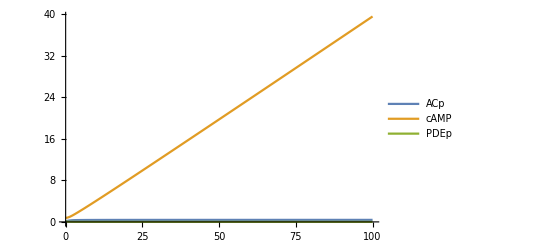

```mathematica
values={ACt->0.39,Km1->2.24,r1->2.84,r2->1.81,Dt->0.10,Km2->3.12,k1->1.07,k2->2.38,E->1.02,r3->0.1,Km3->1.67,r4->3.49,PDEt->0.1};
numericEquations={dACp,dcAMPdT,dPDEpdT}/. values;

systemEquations={ACp'[t]==(numericEquations[[1]]/. {ACp->ACp[t],cAMP->cAMP[t],PDEp->PDEp[t]}),cAMP'[t]==(numericEquations[[2]]/. {ACp->ACp[t],cAMP->cAMP[t],PDEp->PDEp[t]}),PDEp'[t]==(numericEquations[[3]]/. {ACp->ACp[t],cAMP->cAMP[t],PDEp->PDEp[t]})};
solution=NDSolve[{systemEquations,initialConditions},{ACp,cAMP,PDEp},{t,0,100}];

Plot[Evaluate[{ACp[t],cAMP[t],PDEp[t]}/. solution],{t,0,100},PlotLegends->{"ACp","cAMP","PDEp"}]
```

```mathematica
{ACt->1.39,Km1->2.24,r1->1.84,r2->1.81,Dt->1.1,Km2->3.12,k1->1.07,k2->2.38,ⅇ->1.02,r3->0.1,Km3->1.67,r4->3.49,PDEt->0.1}/.Rule->List
```

{{ACt,1.39},{Km1,2.24},{r1,1.84},{r2,1.81},{Dt,1.1},{Km2,3.12},{k1,1.07},{k2,2.38},{ⅇ,1.02},{r3,0.1},{Km3,1.67},{r4,3.49},{PDEt,0.1}}

```mathematica
Plot[Evaluate[{ACp[t],cAMP[t],PDEp[t]}/. solution],{t,0,50},PlotLegends->{"ACp","cAMP","PDEp"}]

RungeKutta4[system_,vars_,initVals_,{t_,tmin_,tmax_,dt_}]:=Module[{k1,k2,k3,k4,n,timeVals,varVals,currentVals},n=Ceiling[(tmax-tmin)/dt];
timeVals=Table[tmin+i*dt,{i,0,n}];
varVals=Table[{},{Length[vars]}];
currentVals=initVals;
Do[k1=dt*system/. Thread[vars->currentVals];
k2=dt*system/. Thread[vars->(currentVals+k1/2)];
k3=dt*system/. Thread[vars->(currentVals+k2/2)];
k4=dt*system/. Thread[vars->(currentVals+k3)];
currentVals=currentVals+1/6*(k1+2*k2+2*k3+k4);
varVals=MapThread[Append,{varVals,currentVals}];,{t,timeVals[[2;;]]}];
Transpose[{timeVals,Sequence@@Transpose[varVals]}]];
```

```mathematica
dt=0.01;(*Fixed time step*)tmin=0;
tmax=50;
initVals={0.1,0.8,0.1};(*Initial conditions for ACp,cAMP,PDEp*)rk4Results=RungeKutta4[numericEquations,{ACp,cAMP,PDEp},initVals,{t,tmin,tmax,dt}];
```

Transpose::nmtx: The first two levels of {{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,«4991»},{0.102352,0.799194,0.0984363},{0.104677,0.798445,0.0968998},{0.106976,0.797751,0.0953899},«4»,{0.118091,0.79508,0.0882202},{0.120241,0.794699,0.0868588},«4991»} cannot be transposed.